```mathematica
(*LaTeX Equation images*)
<<MaTeX`
tex[x_] := Pane[
	MaTeX[x, Magnification->2],
	Full, Alignment->Center]

print[x_] := CellPrint[ExpressionCell[
	Style[TraditionalForm[x], FontSize->20, FontFamily->"TR"], 
	"DisplayFormulaNumbered"]]

(*Set up plot theme*)
Themes`AddThemeRules["abestheme",
	DefaultPlotStyle->Thread@Directive[
		Darker[#]&/@{Blue,Red,Green,Magenta,Cyan,Orange},Thick],
		LabelStyle->Directive[Black, 13, 
			FontFamily-> "Times New Roman"],
	Frame->True, 
	FrameStyle->Directive[Black, 13, FontFamily->"Times New Roman"]];
	
imgdir = "~/Documents/papers/physical-review-e-heterogeneity/";
```

# Representational Rényi Heterogeneity

## Primary Supplemental Analyses

## Abraham Nunes, Martin Alda, Timothy Bardouille, and Thomas Trappenberg Dalhousie University, Halifax, Nova Scotia, Canada

## Introduction

In this supplement, we provide implementation of analyses reported in the main body.

## Existing Heterogeneity Indices

## Numbers Equivalent Heterogeneity Measures

Given a categorical set 𝒳 = {1,2,…, n} with probability distribution p=(p_i)_(i=1,2,…,n) (Jost 2006) has argued that heterogeneity is best measured using the exponential of the Rényi entropy,

```mathematica
assumptions = {∑_(i=1)^n Subscript[p, i]==1, 0≤Subscript[p, i]};
renyiq = Subscript[Π, q][p]==(∑_(i=1)^n Subscript[p, i]^q)^(1/(1-q));
print@renyiq
```

Π_q(p)==(∑_(i=1)^n p_i^q)^(1/(1-q))

a quantity known as the Hill numbers (Hill, 1973) or Rényi heterogeneity (Nunes, Trappenberg, and Alda, 2019), whose parameter q≥0 specifies insensitivity to rare classes. Special cases of Equation (1) include the observed richness (at q=0),

```mathematica
renyi0 = renyiq /. q->0;
print@renyi0
```

Π_0(p)==n

the exponential of Shannon entropy (Shannon, 1948), which is related to \textit{perplexity}, at lim_(q→1) :

```mathematica
(*Step 1: Transform to log space*)
renyi1 = PowerExpand@ApplySides[Log, renyiq];
(*Step 2: Limit as q->1 by L'Hopital's rule*)
renyi1 = #1 == D[Numerator[#2], q]/D[Denominator[#2], q] /. q->1 & @@ renyi1;
(*Step 3: Simplify Normalization factor*)
renyi1 = #1 == FullSimplify[#2 , 
	Assumptions->assumptions]& @@renyi1;
(*Step 4: Exponential form*)
renyi1 = PowerExpand@ApplySides[Exp, renyi1]; print@renyi1
```

Π_1(p)==ⅇ^(-∑_(i=1)^n p_i log(p_i))

the inverse Simpson concentration or effective number of parties (Simpson, 1949; Laakso, 1979) at q=2,

```mathematica
simpson = renyiq /.q->2; print@simpson
```

Π_2(p)==1/(∑_(i=1)^n p_i^2)

and the \textit{Berger-Parker Diversity} index as q→∞:

```mathematica
(*Step 1: Move to log space*)
bpi = renyiq /. Subscript[p, i]^q->max[p]^q( Subscript[p, i]/max[p])^q ;
(*Step 2: Rearrange terms*)
bpi = bpi /. {
	(∑_(i=1)^n max[p]^q (Subscript[p, i]/max[p])^q)^(1/(1-q))-> max[p]^(q/(1-q))(∑_(i=1)^n (Subscript[p, i]/max[p])^q)^(1/(1-q))
};
(*Print intermediate step*)
print[
	#1 == 
		(HoldForm[lim_(q->∞) #]&@#2[[1]])
		((HoldForm[lim_(q->∞) #]&@Extract[#2[[2]],1])^Extract[#2[[2]], 2])
		&@@bpi]
(*The second term goes to 0*)
bpi = #1 == #2[[1]] &@@ bpi;
(*Go to Log space*)
bpi = PowerExpand@ApplySides[Log, bpi];
(*Now use L'Hopital's rule*)
bpi = #1 == D[Numerator[#2], q]/D[Denominator[#2], q] &@@ bpi;
bpi = bpi /. q->∞;
bpi = ApplySides[Exp, bpi];
print@bpi
```

Π_q(p)==((max(p))^(q/(1-q))q∞) ((∑_(i=1)^n (p_i/(max(p)))^q)q∞)^(1/(1-q))

Π_∞(p)==1/(max(p))

There are two unique properties of the family defined by Equation \ref{eq:renyi-heterogeneity}. First is satisfaction of the replication principle (Botta-Dukat, 2018), which states that if M equally heterogeneous systems with non-overlapping domains are pooled, the aggregated system’s heterogeneity is simply M-fold larger than that of one of the subsystems.

APPENDIX: Rényi heterogeneity and the replication principle

PROPOSITION 1.  Rényi heterogeneity obeys the replication principle.

Proof. The Rényi heterogeneity for a single distribution p=(p_i)_(i=1,2,…,n_i), where n_i∈ℕ_+ is the size of the state space in system i, is

```mathematica
renyiqi = Subscript[Π, q][Subscript[p, i]] == (∑_(j=1)^Subscript[n, i] Subscript[p, i,j]^q)^(1/(1-q));
print@renyiqi
```

Π_q(p_i)==(∑_(j=1)^n_i p_(i,j)^q)^(1/(1-q))

and for the pooled system is

```mathematica
renyiqgamma = Subscript[Π, q][p̄] == (∑_(i=1)^M ∑_(j=1)^Subscript[n, i] (Subscript[p, i,j]/M)^q)^(1/(1-q));
print@renyiqgamma
```

Π_q(p̄)==(∑_(i=1)^M ∑_(j=1)^n_i ((p_(i,j))/M)^q)^(1/(1-q))

The replication principle states the following:

```mathematica
replic = renyiqgamma[[1]] == M renyiqi[[1]]; print@replic
replic = renyiqgamma[[2]] == M renyiqi[[2]]; 
replic = ApplySides[PowerExpand, replic] /.{
	(∑_(i=1)^M ∑_(j=1)^Subscript[n, i] M^-q Subscript[p, i,j]^q)^(1/(1-q)) -> (M^-q∑_(i=1)^M ∑_(j=1)^Subscript[n, i] Subscript[p, i,j]^q)^(1/(1-q))}; print@replic
```

Π_q(p̄)==M Π_q(p_i)

(M^-q ∑_(i=1)^M ∑_(j=1)^n_i p_(i,j)^q)^(1/(1-q))==M (∑_(j=1)^n_i p_(i,j)^q)^(1/(1-q))

Now letting λ_i=∑_(j=1)^n_i p_(i,j)^q and recalling that  λ_i=λ_k ∀i,k∈{1,2,…, M}, we have the following:

```mathematica
replic = replic /.{∑_(j=1)^Subscript[n, i] Subscript[p, i,j]^q->Subscript[λ, i]};
replic = replic /.{
	(M^-q ∑_(i=1)^M Subscript[λ, i])^(1/(1-q))->(M^(1-q)Subscript[λ, i])^(1/(1-q))}; 
replic = replic /.{
	∑_(i=1)^M ∑_(j=1)^Subscript[n, i] Subscript[p, i,j]^q->M Subscript[λ, i]}; print@replic
replic = PowerExpand@replic;print@replic
```

(λ_i M^(1-q))^(1/(1-q))==M λ_i^(1/(1-q))

True

Second, this family is measured in terms of the size of a system’s event space or domain of support: a set of units known as ``numbers equivalent’’ (Patil & Taillie, 1982). The numbers equivalent of a system A is the number of partitions in a uniformly distributed system B whose heterogeneity is equal to A. Jost (2006) noted that each heterogeneity level defines an ``equivalence class’’ of systems within which there exists (abstractly) a uniformly distributed categorical set whose domain size is the index.

BRIEF ASIDE: THE NUMBERS EQUIVALENT
Consider a set 𝒳 with probability distribution p = (p_i)_(i=1)^(n_c^(p)) and Rényi heterogeneity

Π_q[p]=(∑_(i=1)^(n_c^(p)) p_i^q)^(1/(1-q))

A second set 𝒳' with a uniform distribution u_j=1/n_c^(u) ∀j∈{1, 2, …, n_c^(u)} and heterogeneity such that Π_q[p]=Π_q[u] yields

```mathematica
neq = PowerExpand@((∑_(i=1)^(Subscript[n, c]^p) Subscript[p, i]^q)^(1/(1-q))==(∑_(j=1)^(Subscript[n, c]^(u)) Subscript[u, j]^q)^(1/(1-q))/.Subscript[u, j]->1/Subscript[n, c]^(u));
print@neq
```

(∑_(i=1)^(n_c^p) p_i^q)^(1/(1-q))==n_c^(-((q-1) u)/(1-q))

```mathematica
print@FullSimplify[neq]
```

n_c^u==(∑_(i=1)^(n_c^p) p_i^q)^(1/(1-q))

Thus,  heterogeneity of 𝒳 is equal to the number of partitions n_c^(u) in an equally heterogeneous and uniformly distributed set 𝒳'.

One benefit of using the Rényi heterogeneity family is that its units are always interpretable in terms of physical sizes, rather than the myriad interpretations of other indices (Daly et al., 2018). This may also facilitate comparison across studies, since the behaviour of the Rényi heterogeneity is consistent. 

A second benefit of Rényi heterogeneity is that it may be easily transformed into many other indices of heterogeneity (Crooks, 2018) and inequality (Jost 2010; Eliazar & Sokolov, 2012). Thus, the Rényi heterogeneity family offers an accessible and rich set of descriptors for the measurement of heterogeneity in practice.

## Numbers Equivalent Measures for Non-Categorical Spaces

Many real-world datasets do not conform to the chief assumption of Equation \ref{eq:renyi-heterogeneity}: that the intrinsic geometry of a system is discrete. Several ecological measures of non-categorical heterogeneity thus attempt to relax the restrictive discrete metric assumption. On account of the benefits outlined in  Section \ref{ss:numbers-equivalent}, we focus only on those measured in units of numbers equivalent.

### Preliminaries

The measures reviewed in this section all require a discrete probability distribution p=(p_i)_(i=1,2,…,n) over n∈ℕ_+ categories, and an n×n matrix of pairwise distances, D=(d_(i,j))_(i=1,2,…,n)^(j=1,2,…,n), between categories. For the examples in this section, we are required to model metric and ultrametric distances, which we do for a simple system with n=3 states.

APPENDIX: Parameterized Distance Matrix Setup

DEFINITION 1 (METRIC DISTANCE). The function d:𝒳×𝒳→ℝ_(≥0) is a metric iff the following conditions are satisfied ∀(x,y, z) ∈𝒳:
1. Non-negativity: d(x, y)≥0
2. Identity of indiscernibles: d(x, y)=0 ⟺x=y
3. Symmetry: d(x, y)=d(y, x)
4. Triangle inequality: d(x, y)≤d(x, z)+d(z,y)

DEFINITION 2 (ULTRAMETRIC DISTANCE). The function d:𝒳×𝒳→ℝ_(≥0) is ultrametric iff conditions 1-3 in Definition 1 are satisfied ∀(x,y, z) ∈𝒳 in addition to the ultrametric triangle inequality:  d(x, y)≤max {d(x, z),d(z,y)}.

We define the following paramterized distance matrix for a simple n=3 state system:

```mathematica
(* Specify vertices of a triangle *)
triangle[h_, b_:1] := {{-1/2 b,0},{1/2 b,0},{0,h}};
(* Compute pairwise distances *)
tridist = FullSimplify[DistanceMatrix[
	triangle[h, b], DistanceFunction->EuclideanDistance], 
	Assumptions->{h>0, b>0}];
```

```mathematica
dmtx[h_, b_:1] := ({{0, b, √(b^2/4+h^2)}, {b, 0, √(b^2/4+h^2)}, {√(b^2/4+h^2), √(b^2/4+h^2), 0}})
```

We also define a function to evaluate whether the distance matrix is ultrametric:

```mathematica
UltrametricInequality[d_]:= Flatten[Table[
			d[[i,j]]≤Max[{d[[i,k]], d[[k,j]]}],
			{i,3}, {j,3}, {k,3}]]
UltrametricQ[d_] := AllTrue[UltrametricInequality[d], # == True &]
```

Given the assumptions that h>0 and b>0, there is only one inequality determining the ultrametricity of the distance function:

```mathematica
umineq = DeleteDuplicates[FullSimplify[
			UltrametricInequality[dmtx[h,b]], 
			Assumptions->{h>0, b>0}]][[2]];
print@umineq
```

2 b≤√(b^2+4 h^2)

We also define a standardized version of the distance matrix which rescales values to the 0-1 range:

```mathematica
dstd[h_, b_:1] := Piecewise[{{dmtx[h,b]/(√(b^2/4+h^2)), h ≥ b √3/2}, {dmtx[h,b]/b, True}}]
```

The distance matrix is as follows:

```mathematica
print[Subscript[𝔻, tri][h,b] == MatrixForm[tridist]]
```

𝔻_tri(h,b)==(0 | b | √(b^2/4+h^2)
b | 0 | √(b^2/4+h^2)
√(b^2/4+h^2) | √(b^2/4+h^2) | 0)

and it will be ultrametric when

```mathematica
umineq = ApplySides[
	PowerExpand@Sqrt[(#^2 - b^2)/4]&, umineq];
print@umineq
```

(√3 b)/2≤h

At b √3/2≤h, the triangle becomes isosceles and the distance ultrametric.

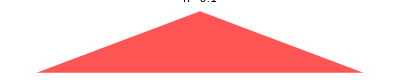
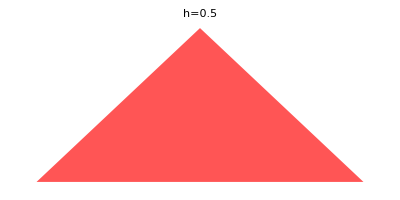
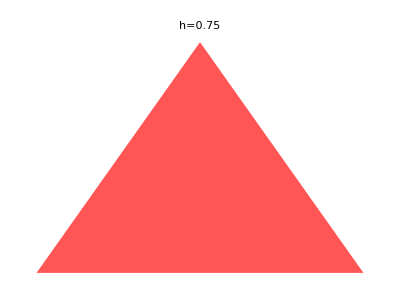
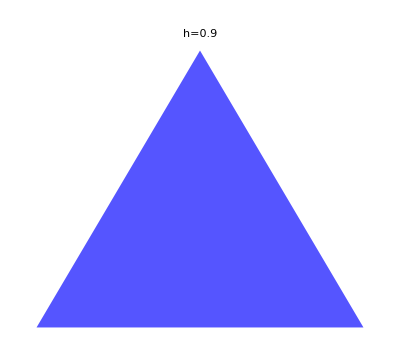
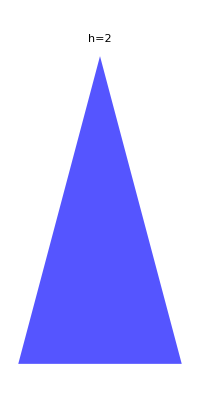
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
umcolor[h_]:=Piecewise[{{Lighter@Blue, UltrametricQ[dmtx[h]]}, {Lighter@Red, ¬UltrametricQ[dmtx[h]]}}]
isoscelesfig = Grid[ArrayReshape[Table[Graphics[{umcolor[h], 
	Triangle[triangle[h]]}, 
	PlotLabel->Style["h="<>ToString[h], Black], 
	ImageSize->Tiny], 
	{h, {0.1, 0.5, 0.75, 0.9, 2, 10}}], {2, 3}]];
isoscelesfig[[1,2,3]] = SwatchLegend[Lighter@{Red, Blue}, 
		{"Non-Ultrametric", "Ultrametric"}];
isoscelesfig
Export["~/Desktop/isoscelesfig.pdf", 
		isoscelesfig, 
		"AllowRasterization"->True];
```

The probability distribution over the states is defined as

```mathematica
pr[κ_] := Table[κ^((i-1)/2)/(1+√κ+κ), {i, 3}]
prob[κ_]:= Piecewise[{{pr[κ], κ>0}, {{1, 0, 0}, κ==0}}];

print[p[κ] == prob[κ]]
```

p(κ)==(Piecewise[{{{1/(κ+√κ+1),(√κ)/(κ+√κ+1),κ/(κ+√κ+1)}, κ>0}, {{1,0,0}, κ==0}}])

```mathematica
(*Verify that it sums to 1*)
FullSimplify[Total[prob[κ]], 
	Assumptions->κ>0] == 1
```

True

where the 1≤κ parameter governs the skewness of the distribution (Figure XX).

```mathematica
pdistdemofig = BarChart[
	Table[prob[κ], {κ, {1, 2, 10, 100}}], 
	PlotLabel->Style["Plot of p[κ]={κ^((i - 1)/2)(κ + √κ+1)^-1}_(i = 1)^3", Black],
	ChartStyle->{Darker/@{Blue, Red, Green, Magenta,Cyan,Orange}, None}, 
	ChartLabels-> {
		Table["κ="<>ToString[κ], 
			{κ, {1, 2, 10, 100}}], 
		None},
	Frame->True, FrameStyle->Directive[Black], 
	FrameLabel->{"Inequality Level (κ)", "Probability"},
	BaseStyle->{FontFamily->"Times New Roman", FontSize->13}, 
	ImageSize->300];
```

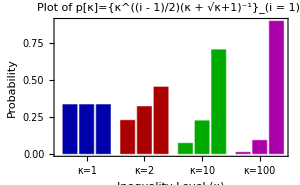
(A) Ultrametric Distance
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | 

(B) Probability Distribution
-Graphics-

```mathematica
distanceprobgrid = Grid[{{
Style["(A) Ultrametric Distance", Bold,15, 
		FontFamily->"Times New Roman"]
}, {isoscelesfig}, 
{},
{Style["(B) Probability Distribution", Bold,15,
	FontFamily->"Times New Roman"]},
{pdistdemofig}}]
Export["~/Desktop/distanceprobgrid.pdf", 
		distanceprobgrid, 
		"AllowRasterization"->True];
```

For the heterogeneity indices that follow, we derive forms that are functions of the distance matrix parameter h and the inequality level κ.

### Indices Based on Rao’s Quadratic Entropy

Rao (1982) introduced a quadratic entropy that was later generalized into a power mean by Chiu & Chao (2014):

```mathematica
grqe = Subscript[Q, q][d,p] == ∑_(i=1)^n ∑_(j=1)^n Subscript[d, i,j](Subscript[p, i] Subscript[p, j])^q;
print@grqe
```

Q_q(d,p)==∑_(i=1)^n ∑_(j=1)^n d_(i,j) (p_i p_j)^q

```mathematica
rqe[q_][d_,p_] := ∑_(i=1)^Length[p] ∑_(j=1)^Length[p] d[[i,j]](p[[i]]p[[j]])^q
```

APPENDIX: Parameterized version of RQE

The parameterized form of RQE in terms of κ>1 and h>0 is

```mathematica
rqeass = {q≥0, h>0, κ>1};
paramrqe = FullSimplify[rqe[q][dmtx[h], pr[κ]], 
	Assumptions->{q≥0, h>0, κ>1}];
print@paramrqe
```

κ^(q/2) (κ+√κ+1)^(-2 q) (√(4 h^2+1) (κ^(q/2)+κ^q)+2)

```mathematica
Qpar[q_][κ_, h_]:=(κ^(q/2)  (2+√(1+4 h^2) (κ^(q/2)+κ^q)))/(1+√κ+κ)^(2 q)
```

Figure XX shows the relationship between RQE and the parameters κ,h.

```mathematica
Grid[ArrayReshape[{
	Table[Show[
		Plot3D[Qpar[q][κ, h], {κ, 1, 10}, {h, 0,Sqrt[3]/2}, 
			PlotStyle->Lighter@Red,
			PlotTheme->"abestheme"],
		Plot3D[Qpar[q][κ, h], {κ, 1, 10}, {h, Sqrt[3]/2, 5},
			PlotStyle->Lighter@Blue,
			PlotTheme->"abestheme"], 
		ImageSize->200, 
		PlotLabel->"Q_q[d,p] at q="<>ToString[q],
		AxesLabel->{"κ", "h"}], 
	{q, {0, 1, 5}}], 
		SwatchLegend[Darker/@{Red, Blue}, 
			{"Non-Ultrametric", "Ultrametric"}]}, 
{2, 2}]]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- |

The RQE is the expected value of pairwise distances between states in the system given matrix D and probability distribution p over states.  The units of RQE are distance, and it will grow without bound as the pairwise distances in D increase.

#### Numbers Equivalent Rao’s Quadratic Entropy

Ricotta & Szeidl (2009) derived an expression of RQE in numbers equivalent based on the fact that

```mathematica
qneq1 = grqe /. {q->1, Subscript[d, i,j]->(1-Subscript[δ, i,j]), d->1-Ι}; 
print@qneq1
```

Q_1(1-Ι,p)==∑_(i=1)^n ∑_(j=1)^n p_i p_j (1-δ_(i,j))

where δ_(i,j) is Kronecker’s delta. Simplifying (22) yields the Gini-Simpson index,

```mathematica
qneq2 = qneq1 /. ∑_(i=1)^n ∑_(j=1)^n Subscript[p, i] Subscript[p, j] (1-Subscript[δ, i,j]) -> 1 - ∑_(i=1)^n Subscript[p, i]^2;
print@qneq2
```

Q_1(1-Ι,p)==1-∑_(i=1)^n p_i^2

which can be converted into Rényi heterogeneity by rearranging (23) and substituting into (4).

```mathematica
print[Subscript[Π, 2][p]==1/(1-#1) &@@qneq2]
```

Π_2(p)==1/(1-Q_1(1-Ι,p))

We then generalize the distance matrix from 1-Ι but rescale it such that ∀_(i,j) 0≤d_(i,j)≤1, as in the categorical case.

```mathematica
print[Subscript[Π, 2][p]==1/(1-#1) &@@  qneq2]
```

Π_2(p)==1/(1-Q_1(1-Ι,p))

APPENDIX: Parameterized Numbers Equivalent RQE

The numbers equivalent RQE expressed in terms of κ and h is

```mathematica
FullSimplify[1/(1-pr[κ].dstd[h,b].pr[κ]), Assumptions-> h≥ (√3)/2 b]
```

1/(1-(2 √κ ((2 b)/(√(b^2+4 h^2))+√κ+κ))/(1+√κ+κ)^2)

```mathematica
FullSimplify[1/(1-pr[κ].dstd[h,b].pr[κ]), Assumptions-> h< (√3)/2 b]
```

1/(1-(2 b √κ+√(b^2+4 h^2) (1+√κ) κ)/(b (1+√κ+κ)^2))

```mathematica
QneqPar[κ_, h_,b_:1]:= Piecewise[{{1/(1-(2 √κ ((2 b)/(√(b^2+4 h^2))+√κ+κ))/(1+√κ+κ)^2), h≥ (√3)/2 b}, {1/(1-(2 b √κ+√(b^2+4 h^2) (1+√κ) κ)/(b (1+√κ+κ)^2)), h <(√3)/2 b}}];
```

```mathematica
neqrqefig = Legended[Show[
	Plot3D[QneqPar[κ, h], {κ, 1, 10}, {h, 0, Sqrt[3]/2},
			PlotStyle->Lighter@Red,
			PlotTheme->"abestheme",  
			ImageSize->300,
			AxesLabel->{"κ", "h", "(Q̂)_e"}],
	Plot3D[QneqPar[κ, h], {κ, 1, 10}, {h, Sqrt[3]/2, 5},
			PlotStyle->Lighter@Blue,
			PlotTheme->"abestheme", 
			ImageSize->300,
			PlotLabel->"Q_q[d,p] at q="<>ToString[q],
			AxesLabel->{"κ", "h", "(Q̂)_e"}]],
		Placed[Framed[SwatchLegend[Darker/@{Red, Blue}, 
			{"Non-Ultrametric", "Ultrametric"}], 
			Background->Opacity[0.6, White]], 
			{0.7, 0.6}]];
Export["~/Desktop/neqrqefig.png", 
		neqrqefig, 
		ImageResolution->500,
		"AllowRasterization"->True];
```

```mathematica
neqrqelines = Legended[Show[
	ListLinePlot[Table[{h, QneqPar[κ, h]}, {κ, 1, 10, 1}, {h, 0, Sqrt[3]/2, 0.01}],
			PlotStyle->Table[{ColorData["ThermometerColors"][(κ-1)/(10-1)], Dashed}, {κ, 1, 10}],
			PlotTheme->"abestheme",  
			ImageSize->300,
			FrameLabel->{"h", "(Q̂)_e"}],
	ListLinePlot[Table[{h, QneqPar[κ, h]}, {κ, 1, 10,1}, {h, Sqrt[3]/2, 5, 0.01}],
			PlotStyle->Table[{ColorData["ThermometerColors"][(κ-1)/(10-1)]}, {κ, 1, 10}],
			PlotTheme->"abestheme", 
			ImageSize->300,
			PlotLabel->"Q_q[d,p] at q="<>ToString[q],
			FrameLabel->{"h", "(Q̂)_e"}], PlotRange->{{0, 5}, {1.25, 3.1}}],
		{Placed[Framed[LineLegend[{Dashed, Thick}, 
			{"Non-Ultrametric", "Ultrametric"}], 
			Background->Opacity[0.6, White]], 
			{0.7, 0.8}], 
			BarLegend[{"ThermometerColors", {1, 10}}, 
			LegendLabel->"κ", 
			LabelStyle->{Black, FontFamily->"Times New Roman"}]}];
Export["~/Desktop/neqrqelines.pdf", 
		neqrqelines, 
		"AllowRasterization"->True];
```

In the Appendix, we show that the maximal value of (Q̂)_e in the present case is n=3, as expected, and occurs at the ultrametric transition point. We also show that the value of  (Q̂)_e in the limit of skewness (κ→∞) is 1. However, in the limit of distance in the present example, (Q̂)_e→4/9, whereas intuition suggests that as one vertex of a triangle is pulled further away, the effective number of states should approach 2 (since the two other vertices become ever closer). Finally, Figure XX shows the behaviour of the numbers equivalent RQE across different levels of inequality in the pairwise distances and probability distribution over states. One can see that the behaviour of numbers equivalent RQE is categorically different depending on whether the distance function is ultrametric or non-ultrametric. This may be problematic in cases where the ultrametric property cannot be guaranteed.

```mathematica
neqrqefig
```

-Graphics-

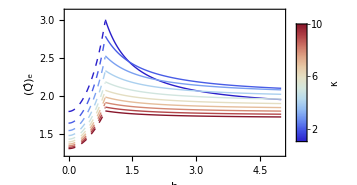

```mathematica
neqrqelines
```

#### Functional Hill Numbers

Chiu & Chao (2014) derived the functional Hill numbers

```mathematica
fhn = Subscript[F, q][d,p] == (Extract[grqe,2]/Extract[grqe/.q->1, 2])^(1/(2(1-q)));
print@fhn
```

F_q(d,p)==((∑_(i=1)^n ∑_(j=1)^n d_(i,j) (p_i p_j)^q)/(∑_(i=1)^n ∑_(j=1)^n p_i p_j d_(i,j)))^(1/(2 (1-q)))

Unfortunately, when ∀_(i,j)p_i=p_j, then F_q(d,p)=n. That is, when all states are equally likely, the functional Hill numbers are insensitive to their dissimilarities.

APPENDIX: Functional Hill numbers (Insensitivity and Parameterization)

PROPOSITION 2.  The functional Hill numbers always equal n when the distribution over states is uniform.

Proof.

```mathematica
fhnp2 = fhn /. {Subscript[p, i]->1/n, Subscript[p, j]->1/n};
print@fhnp2
```

F_q(d,p)==((∑_(i=1)^n ∑_(j=1)^n (1/n^2)^q d_(i,j))/(∑_(i=1)^n ∑_(j=1)^n (d_(i,j))/n^2))^(1/(2 (1-q)))

```mathematica
fhnp2 = fhnp2 /. {(∑_(i=1)^n ∑_(j=1)^n (1/n^2)^q Subscript[d, i,j])/(∑_(i=1)^n ∑_(j=1)^n Subscript[d, i,j]/n^2)->(n^(-2q)∑_(i=1)^n ∑_(j=1)^n Subscript[d, i,j])/(n^-2 ∑_(i=1)^n ∑_(j=1)^n Subscript[d, i,j])};
print@fhnp2
fhnp2 = FullSimplify@PowerExpand@fhnp2;
print@fhnp2
```

F_q(d,p)==(n^(2-2 q))^(1/(2 (1-q)))

n==F_q(d,p)

□

The F_q can be expressed in terms of κ and h as follows for q≠1:

```mathematica
fqpar = Subscript[f, q][κ,h] == FullSimplify[((Qpar[q][κ, h])/(Qpar[1][κ, h]))^(1/(2(1-q)))]
```

f_q[κ,h]==((κ^(1/2 (-1+q)) (1+√κ+κ)^(2-2 q) (2+√(1+4 h^2) (κ^(q/2)+κ^q)))/(2+√(1+4 h^2) (√κ+κ)))^(1/(2-2 q))

To obtain F_1, we must take the limit as q→1, which we do with L’Hopital’s rule.

```mathematica
fqpar1 = PowerExpand@ApplySides[Log, fqpar];
fqpar1 = 
	(#1/.q->1) == Limit[D[Numerator[#2],q]/D[Denominator[#2],q], q->1] &@@fqpar1;
fqpar1 = ApplySides[Exp, fqpar1];
print@fqpar1
```

f_1(κ,h)==exp(1/2 (-(√(4 h^2+1) (κ log(κ)+1/2 √κ log(κ)))/(√(4 h^2+1) (κ+√κ)+2)-(log(κ))/2+2 log(κ+√κ+1)))

```mathematica
F[q_][κ_, h_] :=Piecewise[{{((κ^(1/2 (-1+q)) (1+√κ+κ)^(2-2 q) (2+√(1+4 h^2) (κ^(q/2)+κ^q)))/(2+√(1+4 h^2) (√κ+κ)))^(1/(2-2 q)), q≠1}, {ⅇ^(1/2 (-Log[κ]/2-(√(1+4 h^2) (1/2 √κ Log[κ]+κ Log[κ]))/(2+√(1+4 h^2) (√κ+κ))+2 Log[1+√κ+κ])), q==1}}]
```

Figure XX shows the relationship between F_q and the parameters κ,h.

```mathematica
fhnfig = Grid[ArrayReshape[{
	Table[Show[
		Plot3D[F[q][κ, h], {κ, 1, 2}, {h, 0,Sqrt[3]/2}, 
			PlotStyle->Lighter@Red,
			PlotTheme->"abestheme"],
		Plot3D[F[q][κ, h], {κ, 1, 2}, {h, Sqrt[3]/2, 2},
			PlotStyle->Lighter@Blue,
			PlotTheme->"abestheme"], 
		ImageSize->200, 
		PlotLabel->"F_q[d,p] at q="<>ToString[q],
		AxesLabel->{"κ", "h"}], 
	{q, {0, 1, 5}}], 
		SwatchLegend[Darker/@{Red, Blue}, 
			{"Non-Ultrametric", "Ultrametric"}]}, 
{2, 2}]];
Export["~/Desktop/fhnfig.png", 
		fhnfig, 
		ImageResolution->500,
		"AllowRasterization"->True];
```

```mathematica
fhnlines = Grid[{ 
		Catenate[{Table[Show[ListLinePlot[Table[{h, F[q][κ, h]}, {κ, 1, 2, 0.1}, {h, 0,Sqrt[3]/2, 0.01}], 
			PlotStyle->Table[{ColorData["ThermometerColors"][(κ-1)/(2-1)], Dashed}, {κ, 1, 2, 0.1}],
			PlotTheme->"abestheme", Axes->False], 
			ListLinePlot[Table[{h, F[q][κ, h]}, {κ, 1, 2, 0.1}, {h, Sqrt[3]/2, 2, 0.01}],
			PlotStyle->Table[{ColorData["ThermometerColors"][(κ-1)/(2-1)], Thick}, {κ, 1, 2, 0.1}],
			PlotStyle->Lighter@Blue,
			PlotTheme->"abestheme", Axes->False], 
		PlotRange->Full, 
		ImageSize->300, 
		PlotLabel->"F_q[d,p] at q="<>ToString[q],
		FrameLabel->{"h", "F_q[d,p]"}], 
	{q, {0, 1, 5}}], 
	{BarLegend[{"ThermometerColors", {1, 2}}, LegendLabel->"κ", LabelStyle->{FontFamily->"Times New Roman", Black}], 
	LineLegend[{Dashed, Thick}, {"Non-Ultrametric", "Ultrametric"}]}}]}];
Export["~/Desktop/fhnlines.pdf", 
		fhnlines, 
		ImageResolution->500,
		"AllowRasterization"->True];
```

Figure XX shows the behaviour of F_q across different levels of inequality in state probability and dissimilarity distributions. Note, as predicted, that at κ=1 (uniform probabilities over states) that F_q(κ,h)=n=3. However, there are some counterintuitive properties to observe. First, F_q in all cases (and most notably in F_0 and F_1) shows some evidence of increase as the state probability distribution becomes more unequal. Moreover, this increase results in F_q(κ,h)>3, which should not occur.

```mathematica
fhnfig
```

-Graphics3D- | -Graphics3D-
-Graphics3D- |

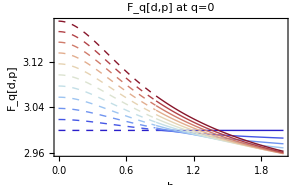
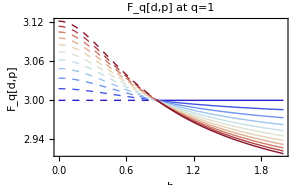
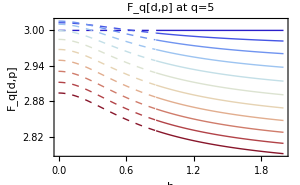
-Graphics- | -Graphics- | -Graphics- |  |

```mathematica
fhnlines
```

### Leinster Cobbold Index

The Leinster-Cobbold Index L_q is defined as

```mathematica
lci = Subscript[L, q][S,p] == (∑_(i=1)^n Subscript[p, i](∑_(j=1)^n Subscript[S, i,j] Subscript[p, j])^(q-1))^(1/(1-q));
print@lci
```

L_q(S,p)==(∑_(i=1)^n p_i (∑_(j=1)^n p_j S_(i,j))^(q-1))^(1/(1-q))

where S is an n×n positive semidefinite similarity matrix, which if replaced by the n×n identity matrix I recovers Rényi heterogeneity:

```mathematica
print[Subscript[L, q][Ι,p] == (∑_(i=1)^n (Subscript[p, i](∑_(j=1)^n Subscript[S, i,j] Subscript[p, j])^(q-1)))^(1/(1-q)) /.{(∑_(j=1)^n Subscript[S, i,j] Subscript[p, j])^(q-1)-> Subscript[p, i]^(q-1)}]
```

L_q(Ι,p)==(∑_(i=1)^n p_i^q)^(1/(1-q))

Here, we obtain the similarity matrix by the transformation S_(i,j)=e^(-u D_(i,j)), where u∈ℝ_(≥0) is a scaling factor. When u=0,  S_(i,j)=1 everywhere. Conversely, when u→∞, S_(i,j)=1 and one can easily verify L_q becomes the Rényi heterogeneity in that case.

APPENDIX: Leinster-Cobbold Index Parametric Form

First we express the similarity matrix.

```mathematica
sim[u_:1][h_,b_:1] := Exp[-u dmtx[h,b]]
```

Now we can compute the LCI in terms of κ,h,u.

```mathematica
lcipar[q_,u_][κ_,h_] := Piecewise[{{(pr[κ].(sim[u][h].pr[κ])^(q-1))^(1/(1-q)), q≠1}, {Product[((sim[u][h].pr[κ])^(-pr[κ]))[[i]],{i, 3}], q==1}}]
```

The limit of L_q as h→∞ is

```mathematica
limlcih =Limit[lcipar[1,u][κ,h],h->Infinity]
```

ConditionalExpression[((ⅇ^-u+√κ)/(1+√κ+κ))^(-(√κ)/(1+√κ+κ)) ((1+ⅇ^-u √κ)/(1+√κ+κ))^(-1/(1+√κ+κ)) (κ/(1+√κ+κ))^(-κ/(1+√κ+κ)),u>0&&κ+κ^(3/2)+κ^2>0]

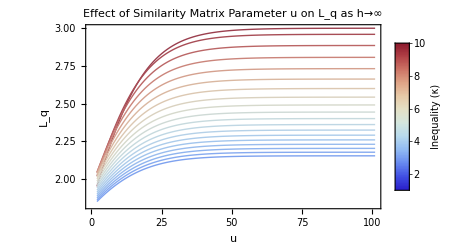

```mathematica
limhinffig = Legended[
	ListLinePlot[Table[limlcih/.u-> 𝓊,
			{κ, 1, 10, 0.5}, 
			{𝓊,0, 10, 0.1}], 
		PlotLabel->"Effect of Similarity Matrix Parameter u on L_q as h→∞",
		ColorFunction->"ThermometerColors", 
		PlotTheme->"abestheme", FrameLabel->{"u", "L_q"}], 
	BarLegend[{"ThermometerColors",{1,10}}, 
	LegendLabel->Style["Inequality (κ)", 
	FontFamily->"Times New Roman"]]]
```

The limit of L_q as κ→∞ should be 1:

```mathematica
limlcik =Limit[lcipar[1,u][κ,h],κ->Infinity]
```

1

The limit of L_q as u→∞ is

```mathematica
limlciu = Limit[lcipar[1,u][κ,h],u->Infinity]
```

ConditionalExpression[((√κ)/(1+√κ+κ))^(-(√κ)/(1+√κ+κ)) (κ/(1+√κ+κ))^(-κ/(1+√κ+κ)) (1+√κ+κ)^(1/(1+√κ+κ)),√(1+4 h^2)>2&&κ+κ^(3/2)+κ^2>0]

The limit of L_q as h→∞ and u→∞ is

```mathematica
limlcihu = Limit[limlcih, u->∞]
```

ConditionalExpression[κ^(-(√κ)/(2 (1+√κ+κ))) (κ/(1+√κ+κ))^(-κ/(1+√κ+κ)) (1+√κ+κ)^((1+√κ)/(1+√κ+κ)),κ+κ^(3/2)+κ^2>0]

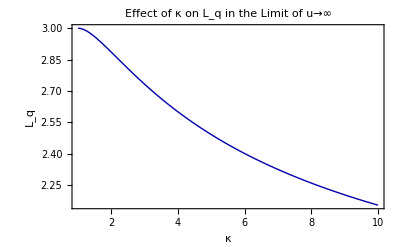

```mathematica
Plot[limlcihu, {κ, 1, 10}, 
	PlotLabel->"Effect of κ on L_q in the Limit of u→∞",
	PlotTheme->"abestheme", FrameLabel->{"κ", "L_q"}]
```

The Leinster-Cobbold index is particularly sensitive to the form of similarity transformation. In the present case, maximal value of the L_q gradually approaches 3 as u grows, while progressively losing sensitivity to distance. Since distances are often easier to compute than similarities, this may be a problem.  Furthermore, in the limit of distance, L_q only approaches the categorical Rényi heterogeneity as u→∞.

## Representational Rényi Heterogeneity

The indices reviewed in Section \ref{ss:existing-non-categorical-indices} were non-parametric generalizations of a categorical heterogeneity measure onto non-categorical spaces. In this section we propose and evaluate two methods that measure Rényi heterogeneity on learned latent representations, rather than on the observable space. There are two main approaches:

Applying Rényi heterogeneity to learned categorical representations

Deriving parametric forms of Rényi heterogeneity for learned non-categorical representations

Both methods employ the same logic, illustrated in Figure XX. Essentially, we learn a model for a posterior distribution on some latent variable z∈𝒵 given observable data x∈𝒳 such that the Rényi heterogeneity is either (A) more scientifically relevant or (B) easier to measure on the latent space.

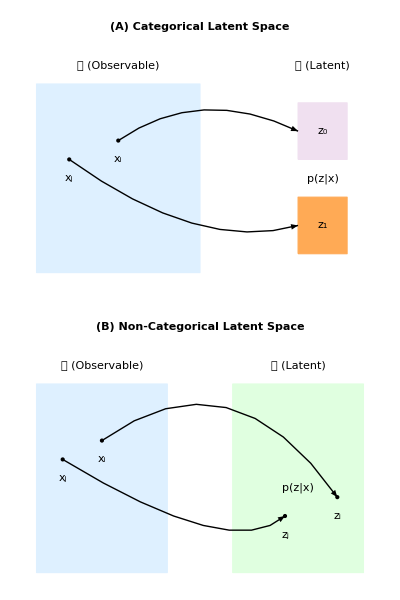

```mathematica
panelA = Show[
	Graphics[{EdgeForm[Thick],LightBlue,Rectangle[{0,0}, {1,1}]}],
	Graphics[{EdgeForm[{Dashed, Thick}], White,Rectangle[{1.5, 0}, {2, 1}]}],
	Graphics[{EdgeForm[{Thick}], Lighter@Orange ,Rectangle[{1.6, 0.1}, {1.9, 0.4}]}],
	Graphics[{EdgeForm[{Thick}], LightPurple ,Rectangle[{1.6, 0.6}, {1.9, 0.9}]}],
	Graphics[Text["𝒳 (Observable)", {0.5, 1.1}]],
	Graphics[Text["𝒵 (Latent)", {1.75, 1.1}]],
	Graphics[{PointSize[Large], Point[{0.5, 0.7}]}],
	Graphics[Text["x_i", {0.5, 0.6}]],
	Graphics[{PointSize[Large], Point[{0.2, 0.6}]}],
	Graphics[Text["x_j", {0.2, 0.5}]],
	Graphics[Text["z_0", {1.75, 0.75}]],
	Graphics[Text["z_1", {1.75, 0.25}]],
	Graphics[{Thick, Arrow[BezierCurve[{{0.5, 0.7}, {1, 1}, {1.6, 0.75}}]]}],
	Graphics[{Thick, Arrow[BezierCurve[{{0.2, 0.6}, {1, 0.1}, {1.6, 0.25}}]]}],
	Graphics[Text["p(z|x)", {1.75, 0.5}]],
	Graphics[Text[Style["(A) Categorical Latent Space", Bold], {1, 1.3}]],
	ImageSize->300,
	BaseStyle->{
		FontFamily->"Times New Roman", 
		FontSize->15}
];
panelB = Show[
	Graphics[{EdgeForm[Thick],LightBlue,Rectangle[{0,0}, {1,1}]}],
	Graphics[{EdgeForm[Thick],LightGreen,Rectangle[{1.5, 0}, {2.5, 1}]}],
	Graphics[Text["𝒳 (Observable)", {0.5, 1.1}]],
	Graphics[Text["𝒵 (Latent)", {2., 1.1}]],
	Graphics[{PointSize[Large], Point[{0.5, 0.7}]}],
	Graphics[Text["x_i", {0.5, 0.6}]],
	Graphics[{PointSize[Large], Point[{2.3, 0.4}]}],
	Graphics[Text["z_i", {2.3, 0.3}]],
	Graphics[{Thick, Arrow[BezierCurve[{{0.5, 0.7}, {1.5, 1.2}, {2.3, 0.4}}]]}],
	Graphics[{PointSize[Large], Point[{0.2, 0.6}]}],
	Graphics[Text["x_j", {0.2, 0.5}]],
	Graphics[{PointSize[Large], Point[{1.9, 0.3}]}],
	Graphics[Text["z_j", {1.9, 0.2}]],
	Graphics[{Thick, Arrow[BezierCurve[{{0.2, 0.6}, {1.5, 0.05}, {1.9, 0.3}}]]}],
	Graphics[Text["p(z|x)", {2., 0.45}]],
	Graphics[Text[Style["(B) Non-Categorical Latent Space", Bold], {1.25, 1.3}]],
	ImageSize->300,
	BaseStyle->{
		FontFamily->"Times New Roman", 
		FontSize->15}
];
reprenyigrid = Grid[{{panelA},{panelB}}]
Export["~/Desktop/reprenyigrid.pdf", 
		reprenyigrid, 
		"AllowRasterization"->True];
```

## Heterogeneity of Learned Categorical Representations

For each of n_s∈ ℕ_+observations of data X=(x_(i,j))_(i=1,2,…,n_s)^(j=1,2,…,n_x)∈𝒳⊆ℝ^n_x, this approach assumes that there exists a latent categorical representation z=(z_(i,))_(i=1,2,…,n_s)∈𝒵={1,2,…,n_c} to which each point in 𝒳 can be mapped (and vice versa). Unlike the indices presented in Section XX, we do not presume that 𝒳→𝒵 is known, and rather seek to learn a parameterized posterior distribution p_θ[z\[Conditioned]X] with which we may compute the Rényi heterogeneity as

Π_q[z\[Conditioned]X]=(∑_𝒵 p_θ^q[z\[Conditioned]X])^(1/(1-q)).

In this section, we contrast this approach with the (Q̂)_e, F_q, and L_q indices introduced in Section XX using a beta mixture model (BMM). We show key elements of the model here, with a more thorough treatment offered in the appendix.

APPENDIX: Beta Mixture Model Setup

A single beta mixture model in the present study is composed of two beta distributions whose indices are latent variables 𝒵={1,2}. The prior distribution over 𝒵 is

```mathematica
prior = {1-c, c};
print[Subscript[p, c][z]==prior]
```

p_c(z)=={1-c,c}

where c is the probability that z=2.  The likelihood function is as follows:

```mathematica
bmmass = assumptions = {0<x<1, 0<α, 0<β, 0<Subscript[α, 1], 0<Subscript[β, 1], 0<Subscript[α, 2], 0<Subscript[β, 2]};
likelihood = FullSimplify[
	Table[Likelihood[BetaDistribution[Subscript[α, i], Subscript[β, i]], {x}], {i, 2}],
	Assumptions->0<x<1];
print[Subscript[p, α,β][x|z] == likelihood]
```

p_(α,β)(x|z)=={(x^(α_1-1) (1-x)^(β_1-1))/α_1β_1,(x^(α_2-1) (1-x)^(β_2-1))/α_2β_2}

Figure XX demonstrates the relationship between these distributions in the case where α_1=β_2 and that α_2=β_1.

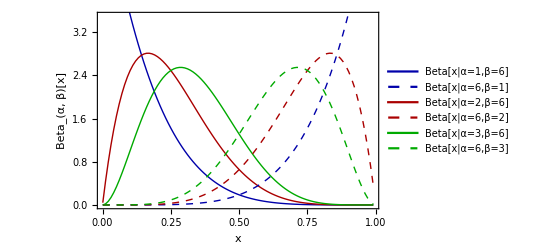

StringJoin::string: String expected at position 1 in imgdir <> \"\<bmmlikfig.pdf\>\".

Export::chtype: First argument imgdir<>bmmlikfig.pdf is not a valid file specification.

```mathematica
bmmlikfig = Legended[Show[
ListLinePlot[
	Table[
		{x, Likelihood[BetaDistribution[α, β], {x}]/.β-> 6},
		{α, 1, 3},{x, 0.001, 0.999, 0.01}],
	PlotTheme->"abestheme"], 
ListLinePlot[
	Table[
		{x, Likelihood[BetaDistribution[β, α], {x}]/.β-> 6},
		{α, 1, 3},{x, 0.001, 0.999, 0.01}],
	], ], ]
Export[imgdir<>"bmmlikfig.pdf",
		bmmlikfig, 
		"AllowRasterization"->True];
```

The marginal distribution over 𝒳 is as follows:

```mathematica
marginal = MixtureDistribution[prior, {BetaDistribution[α, β], BetaDistribution[β, α]}];

print[Subscript[p, c,α,β][x]==FullSimplify[Likelihood[marginal, {x}], Assumptions->assumptions]]
```

p_(c,α,β)(x)==(c (1-x)^(α-1) x^(β-1))/βα-((c-1) x^(α-1) (1-x)^(β-1))/αβ

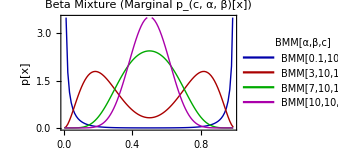

```mathematica
bmmplot= ListLinePlot[
Table[
	{x, (-((-1+c) (1-x)^(-1+β) x^(-1+α))/Beta[α,β]+(c (1-x)^(-1+α) x^(-1+β))/Beta[β,α])/.
	{c->0.5,β->10}}, {α, {0.1, 3, 7, 10}},
	{x, 0.001, 0.999, 0.01}],
PlotLabel->"Beta Mixture (Marginal p_(c, α, β)[x])",
PlotRange->{Automatic, {0, 3.5}},
PlotLegends->LineLegend[
	Table["BMM["<>ToString[α]<>",10,1/2]", {α, {0.1, 3, 7, 10}}], 
	LegendLabel->Style["BMM[α,β,c]", Bold]],
FrameLabel->{"x", "p[x]"},
PlotTheme->"abestheme", ImageSize->250]
```

Substituting α_1=β_2→ α and  α_2=β_1→β , we can compute a posterior distribution over categories.

```mathematica
lik = likelihood/.{Subscript[α, 1]->α, Subscript[β, 1]->β, Subscript[α, 2]->β, Subscript[β, 2]->α};
posterior = FullSimplify[((lik × prior)/(lik.prior)), Assumptions->bmmass];
print[Subscript[p, α,β,c][z|x]==posterior]
```

p_(α,β,c)(z|x)=={1/(1-(c (1/x-1)^(α-β))/(c-1)),1/(1-((c-1) (1/x-1)^(β-α))/c)}

From this point, there are two methods by which data may be assigned to mixture component 1 or 2. First, one could use a hard assignment threshold where ẑ=1 if p(z=1\[Conditioned]x)>p(z=2\[Conditioned]x) and vice versa. Second, one could assign “soft” labels corresponding to p(z\[Conditioned]x) ∀_x. We address both approaches here.

CLUSTER ASSIGNMENT BY HARD THRESHOLDING

After learning the BMM distribution parameters (α,β,c), a hard thresholding approach finds a decision boundary τ_(α,β,c) at which

ẑ=Piecewise[{{1, x≤ τ_(α,β,c)}, {2, x> τ_(α,β,c)}}]

The decision boundary for the BMM is as follows:

```mathematica
bmmthresh = Solve[posterior[[1]]==posterior[[2]], x][[1,1,2]];
bmmthresh = Numerator[#]/(1+Simplify@ExpandAll@Extract[Denominator[#], 2])&@bmmthresh;
print[Subscript[τ, α,β,c]==bmmthresh]
```

τ_(α,β,c)==1/((1/c-1)^(1/(2 α-2 β)) (1-c)^(1/(2 α-2 β)) c^(-1/(2 α-2 β))+1)

```mathematica
thresh[α_,β_,c_] = 1/(1+(-1+1/c)^(1/(2 α-2 β)) (1-c)^(1/(2 α-2 β)) c^(-1/(2 α-2 β)));
```

For a given threshold τ, the probability that the model will assign point x_i to cluster ẑ=2 is given by the Beta mixture marginal survival function evaluated at τ:

```mathematica
bmmsf = FullSimplify[SurvivalFunction[marginal, x], Assumptions->{0<x<1}]
```

-(-1+c) BetaRegularized[x,1,α,β]+c BetaRegularized[x,1,β,α]

```mathematica
sf[α_, β_, c_][x_] := -(-1+c) BetaRegularized[x,1,α,β]+c BetaRegularized[x,1,β,α]
```

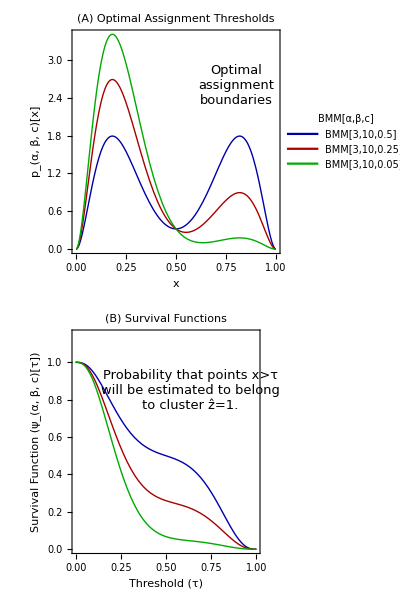

```mathematica
threshplot = Show[Plot[{
	(-((-1+c) (1-x)^(-1+β) x^(-1+α))/Beta[α,β]+(c (1-x)^(-1+α) x^(-1+β))/Beta[β,α])/.{α->3, β->10, c->1/2},
	(-((-1+c) (1-x)^(-1+β) x^(-1+α))/Beta[α,β]+(c (1-x)^(-1+α) x^(-1+β))/Beta[β,α])/.{α->3, β->10, c->1/4},
	(-((-1+c) (1-x)^(-1+β) x^(-1+α))/Beta[α,β]+(c (1-x)^(-1+α) x^(-1+β))/Beta[β,α])/.{α->3, β->10, c->1/20}
	}, {x, 0, 1}, 

	PlotLabel->Style["(A)", Bold]" Optimal Assignment Thresholds",
	GridLines->{{
		{thresh[3,10,1/2], Directive[Darker[Blue], Dashed, Thick]}, 
		{thresh[3,10,1/4],Directive[Darker[Red], Dashed, Thick] }, 
		{thresh[3,10,1/20],Directive[Darker[Green], Dashed, Thick] }}, None},
	FrameLabel->{"x", "p_(α, β, c)[x]"},
	PlotTheme->"abestheme"], 
Graphics[Text[Style["Optimal\nassignment\nboundaries",13,  
	TextAlignment->Left, FontFamily->"Times New Roman"], 
	Scaled[{0.79,0.75}]]],
ImageSize->275];

sfplot = Show[
	Plot[{
		sf[3, 10, 1/2][x],
		sf[3, 10, 1/4][x],
		sf[3, 10, 1/20][x]
	}, {x, 0, 1}, 
	PlotRange->{Automatic, {0, 1.15}},
	PlotLabel->Style["(B)", Bold]" Survival Functions",
	FrameLabel->{"Threshold (τ)", "Survival Function (ψ_(α, β, c)[τ])"},
	PlotTheme->"abestheme"], 
	Graphics[Text[
		Style["Probability that points x>τ\n"<>
			  "will be estimated to belong\n"<>
			  "to cluster ẑ=1.",13,  
			TextAlignment->Left, 
			FontFamily->"Times New Roman"], 
			Scaled[{0.63, 0.73}]]],
	ImageSize->275];

threshsfgrid = Legended[
	Grid[{{threshplot}, {sfplot}}],
	LineLegend[Directive[Darker[#],Thick]&/@{Blue,Red,Green},
		Table[Style["BMM[3,10,"<>ToString[c]<>"]",
				FontFamily->"Times New Roman"], 
		{c, {0.5, 0.25,0.05}}], 
	LegendLabel->Style["BMM[α,β,c]", Bold, 
			FontFamily->"Times New Roman"]]]

Export["~/Desktop/threshsfgrid.pdf", 
		threshsfgrid,
		"AllowRasterization"->True];
```

The vector of posterior marginal probabilities over clusters estimated by our model is  as follows:

p[ẑ]=φ={1-ψ_(α,β,c)[x], ψ_(α,β,c)[x]}

```mathematica
𝒫[α_, β_, c_][x_] := {1-sf[α, β, c][x], sf[α,β,c][x]}
```

Given φ, we can compute the categorical Rényi heterogeneity on the latent space as

Π_q[φ]=Piecewise[{{((1-ψ_(α,β,c)[x])^q+(ψ_(α,β,c)[x])^q)^(1/(1-q)), q≠0∧q≠1∧q≠∞}, {2, q=0}, {ⅇ^(-(1-ψ_(α,β,c)[x])Log[1-ψ_(α,β,c)[x]]-ψ_(α,β,c)[x]Log[ψ_(α,β,c)[x]]), q=1}, {(max{1-ψ_(α,β,c)[x], ψ_(α,β,c)[x]})^-1, q=∞}}].

```mathematica
log [x_]:=Piecewise[{{Log[x], x≠0}, {0, True}}]
renyihet[q_, α_, β_, c_][x_]:= Piecewise[{{Total[(𝒫[α, β, c][x])^q]^(1/(1-q)), q≠0&&q≠1&&q≠∞}, {Exp[-Total[𝒫[α, β, c][x] (log/@𝒫[α, β, c][x])]], q==1}, {2, q==0}, {1/Max[𝒫[α, β, c][x]], q==∞}}]
```

```mathematica
alphas = {9.1, 2};
cprob = {0.1, 0.8};
renyihetgrid = Legended[Grid[{Table[Show[Plot[{
		renyihet[0.1, alphas[[i]],9,cprob[[i]]][x], 
		renyihet[1, alphas[[i]],9,cprob[[i]]][x], 
		renyihet[2,alphas[[i]],9,cprob[[i]]][x], 
		renyihet[∞,alphas[[i]],9,cprob[[i]]][x]},
	{x, 0, 1}, 
	PlotLabel->"α="<>ToString[Round[alphas[[i]]]]<>
				", β=9, c="<>ToString[cprob[[i]]],
	GridLines->{
		{{thresh[alphas[[i]],9,cprob[[i]]], 
		  Directive[Gray, Thick, Opacity[0.5]]}},
		  None},
	PlotTheme->"abestheme", 
	PlotStyle->68,
	PlotRange->Full, 
	FrameLabel->{None, "Π_q[Z|X]"}], 
ListPlot[{
{thresh[alphas[[i]], 9, cprob[[i]]], 
renyihet[0.1, alphas[[i]],9,cprob[[i]]][thresh[alphas[[i]], 9, cprob[[i]]]]},
{thresh[alphas[[i]], 9, cprob[[i]]],
renyihet[1, alphas[[i]],9,cprob[[i]]][thresh[alphas[[i]], 9, cprob[[i]]]]},
{thresh[alphas[[i]], 9, cprob[[i]]],
renyihet[2,alphas[[i]],9,cprob[[i]]][thresh[alphas[[i]], 9, cprob[[i]]]]}, 
{thresh[alphas[[i]], 9, cprob[[i]]],
renyihet[∞,alphas[[i]],9,cprob[[i]]][thresh[alphas[[i]], 9, cprob[[i]]]]}
}, PlotStyle->{Black, PointSize[Medium]}]
], {i, 2}], 
Table[Plot[{
	c((1-x)^(-1+β) x^(-1+α))/Beta[α,β]/.{α->9, β->alphas[[i]], c->cprob[[i]]},
	(1-c)((1-x)^(-1+α) x^(-1+β))/Beta[β,α]/.{α->9, β->alphas[[i]], c->cprob[[i]]},
	sf[2, 9, cprob[[i]]][x]},
	{x, 0, 1}, 
GridLines->{
	{{thresh[alphas[[i]],9,cprob[[i]]], 
	  Directive[Gray, Thick, Opacity[0.5]]}}, 
	  None},
PlotTheme->"abestheme", 
PlotRange->Full, 
FrameLabel->{"x", "p[x]"}],{i,2}]
}], 
{LineLegend[68, Table[Style["q="<>ToString[q],  
FontFamily-> "Times New Roman"], 
{q, {0.1, 1, 2, ∞}}], 
LegendLabel->Style["Rényi Order",Bold, FontFamily-> "Times New Roman"]], 
LineLegend[Darker[#]&/@{Blue, Red, Green}, 
Style[#, FontFamily-> "Times New Roman"]
	&/@{"Beta[α,β,c]", "Beta[β,α,c]", "ψ_(α, β, c)[x]"}, 
LegendLabel->Style["Component\nDistributions", 
					Bold, 
					FontFamily-> "Times New Roman"]]}];
Export["~/Desktop/renyihetgrid.pdf", renyihetgrid, "AllowRasterization"->True];
```

SOFT CLUSTER ASSIGNMENT

In the case of “soft” labeling, one obtains a posterior distribution over clusters for each x. The Rényi heterogeneity for the posterior distribution given x_i is

```mathematica
print[Subscript[Π, q][z\[Conditioned] Subscript[x, i]]==(HoldForm[∑_𝒵 p[z\[Conditioned] Subscript[x, i]]^q])^(1/(1-q))]
```

Π_q(z\[Conditioned]x_i)==(∑_𝒵 (p(z\[Conditioned]x_i))^q)^(1/(1-q))

The Rényi heterogeneity of the pooled set of observations ∀x∈𝒳 is

```mathematica
print[(Subscript[Π, q]^γ)[Z\[Conditioned]X]==(HoldForm[∑_𝒵 (Subscript[𝔼, x\[Distributed]p[x]][p[z\[Conditioned]x]])^q])^(1/(1-q))==(HoldForm[p[z==1]^q+p[z==2]^q])^(1/(1-q))==((1-c)^q+c^q)^(1/(1-q))]
```

Product::prodwarn: Warning: Π_q^γ contains a capital Pi. Use EscprodEsc to enter a product sign.

Π_q^γ(Z\[Conditioned]X)==(∑_𝒵 (𝔼_(x\[Distributed]p(x))(p(z\[Conditioned]x)))^q)^(1/(1-q))==((p(z==1))^q+(p(z==2))^q)^(1/(1-q))==(c^q+(1-c)^q)^(1/(1-q))

Assuming that each value of x∈𝒳 is equally weighted, the average within-observation Rényi heterogeneity is

```mathematica
print[(Subscript[Π, q]^α)[Z\[Conditioned]X]==(HoldForm[∫_0^1 (∑_𝒵 p[z\[Conditioned]x]^q) ⅆx])^(1/(1-q))]
```

Product::prodwarn: Warning: Π_q^α contains a capital Pi. Use EscprodEsc to enter a product sign.

Π_q^α(Z\[Conditioned]X)==(∫_0^1 (∑_𝒵 (p(z\[Conditioned]x))^q)ⅆx)^(1/(1-q))

By Jost’s multiplicative decomposition Π_q^γ=Π_q^α Π_q^β between-observation heterogeneity is thus

```mathematica
print[(Subscript[Π, q]^β)[Z\[Conditioned]X]==(((1-c)^q+c^q)/HoldForm[∫_0^1 (∑_𝒵 p[z\[Conditioned]x]^q) ⅆx])^(1/(1-q))]
```

Product::prodwarn: Warning: Π_q^β contains a capital Pi. Use EscprodEsc to enter a product sign.

Π_q^β(Z\[Conditioned]X)==((c^q+(1-c)^q)/(∫_0^1 (∑_𝒵 (p(z\[Conditioned]x))^q)ⅆx))^(1/(1-q))

which we solve numerically in the present study. For the mixture of two betas example, we have the following between-observation heterogeneity (which we show only for q≠1 here):

```mathematica
betahet[q_][a_,b_,ℼ_]:=(Total[prior^q /. {c->ℼ}]/NIntegrate[Total[posterior^q /. {α->a, β->b, c->ℼ}], {x, 0, 1} ])^(1/(1-q))
```

Since the hard thresholding approach imposes a sharp split between mixture components, we expect that the β-heterogeneity under soft cluster assignments will be lower than the heterogeneity observed under hard thresholding. We compare the two approaches in Figure XX.

General::munfl: (6.2877×10^-11)^100 is too small to represent as a normalized machine number; precision may be lost.

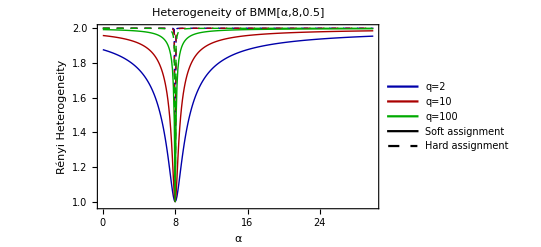

~/Desktop/softvhardfig.pdf

```mathematica
softvhardfig = Legended[Show[
	ListLinePlot[
		Table[{α, renyihet[q, α, 8, 0.499][thresh[α,8,0.499]]}, 
			{q, {2, 10, 100}}, {α, 0.001, 30, 0.1}], 
		PlotTheme->"abestheme", 
		PlotStyle->Dashed, 
		PlotRange->Full],
	ListLinePlot[
		Table[{α, betahet[q][α,8,0.499]}, 
			{q, {2, 10, 100}}, {α, 0.001, 30, 0.1}], 
		PlotTheme->"abestheme", 
		PlotRange->Full], 
	FrameLabel->{"α", "Rényi Heterogeneity"},
	PlotLabel->"Heterogeneity of BMM[α,8,0.5]"], 
	{LineLegend[Darker@{Blue, Red, Green}, {"q=2", "q=10", "q=100"}],
	LineLegend[{Thick, Dashed}, {"Soft assignment", "Hard assignment"}]}]
Export["~/Desktop/softvhardfig.pdf", softvhardfig,
		"AllowRasterization"->True]
```

Note that as the mixture components become more distant from each other (i.e. as |α-β| grows), then Rényi heterogeneity under the soft assignment approach approaches that of the hard thresholding method.

For the purposes of this paper, we define a simple BMM by the following joint distribution:

p_(α,β,c)(x,z)=={(1-c)p(x|z=1),c p(x|z=2)}

where c=p(z=2), and

```mathematica
print[p[x\[Conditioned]z==1]==Subscript[beta, α,β][x]==FullSimplify[PDF[BetaDistribution[α,β],x], Assumptions->0<x<1]]
```

p(x\[Conditioned]z==1)==beta_(α,β)(x)==(x^(α-1) (1-x)^(β-1))/αβ

is the probability density function for beta distribution with label z=1, Β is the beta function, and (α,β) are pseudo-count parameters. For notational and computational parsimony, we define p(x\[Conditioned]z=2)=beta_(β,α)(x).

Assuming that the α,β, and c parameters have been learned for a BMM given data X, we can compute the posterior probability of cluster assignment for point x∈𝒳 as follows:

```mathematica
print[Subscript[p, α,β,c][z\[Conditioned]x]==posterior]
```

p_(α,β,c)(z\[Conditioned]x)=={1/(1-(c (1/x-1)^(α-β))/(c-1)),1/(1-((c-1) (1/x-1)^(β-α))/c)}

One approach to compute the representational Rényi heterogeneity in this case would be to use the p_(α,β,c)(z\[Conditioned]x) values across x∈𝒳 to perform the following decomposition, which follows from the original derivation by Jost (2007):

```mathematica
print[(Subscript[Π, q]^Between)[Z\[Conditioned]X]==((Subscript[Π, q]^Pooled)[Z\[Conditioned]X])/((Subscript[Π, q]^Within)[Z\[Conditioned]X])==(((1-c)^q+c^q)/HoldForm[∫_0^1 (∑_𝒵 p[z\[Conditioned]x]^q) ⅆx])^(1/(1-q))]
```

Product::prodwarn: Warning: Π_q^Between contains a capital Pi. Use EscprodEsc to enter a product sign.

Product::prodwarn: Warning: Π_q^Pooled contains a capital Pi. Use EscprodEsc to enter a product sign.

Product::prodwarn: Warning: Π_q^Within contains a capital Pi. Use EscprodEsc to enter a product sign.

General::stop: Further output of Product::prodwarn will be suppressed during this calculation.

Π_q^Between(Z\[Conditioned]X)==(Π_q^Pooled(Z\[Conditioned]X))/(Π_q^Within(Z\[Conditioned]X))==((c^q+(1-c)^q)/(∫_0^1 (∑_𝒵 (p(z\[Conditioned]x))^q)ⅆx))^(1/(1-q))

However, the integral in the denominator may be expensive to compute. Another approach is to assume the model assigns “hard” component labels over the domain of 𝒳 based on estimation of an optimal assignment threshold τ_(α,β,c) on 𝒳 for which p(z=2\[Conditioned]x)>p(z=1\[Conditioned]x) ∀x>τ_(α,β,c). In the case of the two-component beta mixture model, the assignment threshold is computed deterministically as follows:

```mathematica
print[Subscript[τ, α,β,c][X]==thresh[α,β,c]]
```

τ_(α,β,c)(X)==1/((1/c-1)^(1/(2 α-2 β)) (1-c)^(1/(2 α-2 β)) c^(-1/(2 α-2 β))+1)

The posterior marginal distribution on 𝒵 is given by p[ẑ]={1-ψ_(α,β,c)[τ], ψ_(α,β,c)[τ]}, where ψ_(α,β,c)[τ]=∫_(τ_(α,β,c))^1 p_(α,β,c)[x]ⅆx is the survival function of the BMM marginal distribution on the observable space 𝒳. The resulting representational Rényi heterogeneity is thus

Π_q[Z\[Conditioned]X]=Piecewise[{{((1-ψ_(α,β,c)[τ])^q+(ψ_(α,β,c)[τ])^q)^(1/(1-q)), q≠0∧q≠1∧q≠∞}, {2, q=0}, {ⅇ^(-(1-ψ_(α,β,c)[τ])Log[1-ψ_(α,β,c)[τ]]-ψ_(α,β,c)[τ]Log[ψ_(α,β,c)[τ]]), q=1}, {(max{1-ψ_(α,β,c)[τ], ψ_(α,β,c)[τ]})^-1, q=∞}}].

Figure XX plots the relationship between threshold values and the representational Rényi heterogeneity for two BMM distributions (one where the components overlap completely, and the other where a more clear separation exists). As expected, when the component distributions are indistinguishable (i.e. complete overlap), the representational Rényi heterogeneity is 1. With greater separation of the component distributions, the representational Rényi heterogeneity increases, but remains within the upper bound of 2.

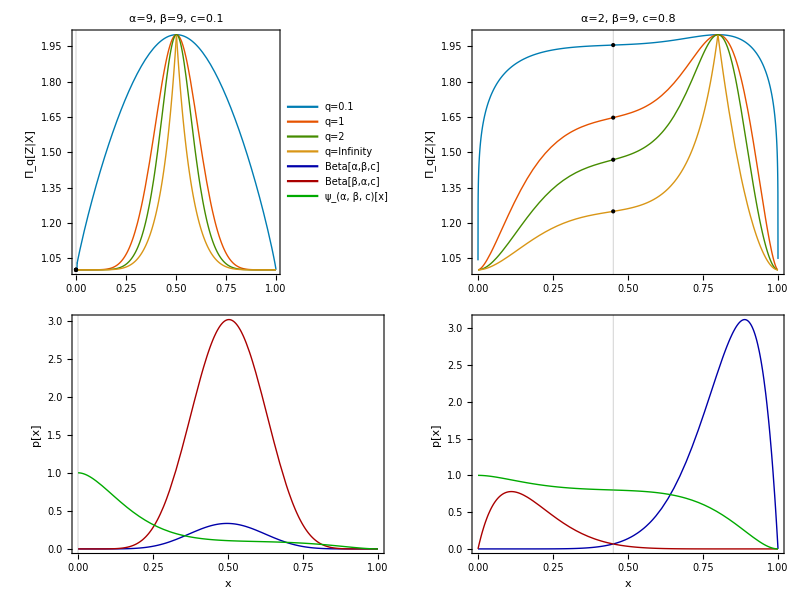

```mathematica
renyihetgrid
```

### Comparison with Existing Heterogeneity Indices

Here, we compare the representational Rényi heterogeneity of a BMM against corresponding values of the numbers equivalent RQE ((Q̂)_e), the functional Hill numbers (F_q), and the Leinster-Cobbold index (L_q). In Appendix XX, we derive closed form expressions for (Q̂)_e, F_q, and L_q under the BMM for comparison to the representational Rényi heterogeneity method.

APPENDIX: Closed form solution for the numbers equivalent RQE, the functional Hill numbers, and the Leinster-Cobbold index under a two-component BMM.

ANALYTICAL EXPRESSION FOR DISTANCE AND SIMILARITY MATRICES UNDER BMM

We must now solve the following integral:

d[x,y]=∫_0^1 ∫_0^1 |x-y|f[x]g[y] ⅆx ⅆy

d[x,y]=∫_0^1 ∫_0^1 |x-y|f[x]g[y] ⅆx ⅆy

where f[x]=Beta_(α,β)[x] and g[x]=Beta_(β,α)[x]. This expands to

d[x,y]= (∫_0^1 ∫_0^1 x f[x]g[y]ⅆxⅆy)_(`term1`)+(∫_0^1 ∫_0^1 y f[x] g[y]ⅆx ⅆy)_(`term2`) -(2∫_0^1 ∫_0^1  min{x, y} f[x]g[y] ⅆx ⅆy)_(`term3`).

```mathematica
assumptions = {0<x<1, 0<y<1, 0<Subscript[α, 1], 0<Subscript[β, 1], 0<Subscript[α, 2], 0<Subscript[β, 2]};
fs[expr_]:=FullSimplify[expr, Assumptions->assumptions]
betapdf[α_, β_][x_]:=((1-x)^(-1+β) x^(-1+α))/Beta[α,β]
int[expr_, {var_, lb_, ub_}]:= Integrate[expr, {var, lb, ub}, Assumptions->assumptions]
```

`term1` is equal to

```mathematica
term1 = int[int[fs[x betapdf[Subscript[α, 1], Subscript[β, 1]][x] betapdf[Subscript[α, 2], Subscript[β, 2]][y]], {x, 0, 1}], {y, 0, 1}]
```

α_1/(α_1+β_1)

and `term2` is

```mathematica
term2 = int[int[fs[y betapdf[Subscript[α, 1], Subscript[β, 1]][x] betapdf[Subscript[α, 2], Subscript[β, 2]][y]], {x, 0, 1}], {y, 0, 1}]
```

α_2/(α_2+β_2)

```mathematica
term1 + term2
```

α_1/(α_1+β_1)+α_2/(α_2+β_2)

so Equation (8) reduces to

d[x,y]= ⟨x⟩+⟨y⟩-(2∫_0^1 ∫_0^1  min{x, y} f[x]g[y] ⅆx ⅆy)_(`term3`).

Integrating the third term requires some rearrangement:

term3=2∫_0^1 ∫_0^1  min{x, y} f[x]g[y] ⅆx ⅆy

term3=2((∫_0^1 ∫_0^y  x f[x]g[y] ⅆx ⅆy)_(`term3a`)+(∫_0^1 ∫_y^1  y f[x]g[y] ⅆx ⅆy)_(`term3b`))

`term3a` evaluates to the following:

```mathematica
term3a = int[int[fs[x betapdf[Subscript[α, 1], Subscript[β, 1]][x] betapdf[Subscript[α, 2], Subscript[β, 2]][y]], {x, 0, y}], {y, 0, 1}]
```

ConditionalExpression[(Gamma[1+α_1] Gamma[1+α_1+α_2] Gamma[β_2] HypergeometricPFQRegularized[{1+α_1,1+α_1+α_2,1-β_1},{2+α_1,1+α_1+α_2+β_2},1])/(Beta[α_1,β_1] Beta[α_2,β_2]),β_1∉ℤ]

We verify that this is correct by comparing to numerical integration

```mathematica
term3a/.{Subscript[α, 1]->9, Subscript[β, 1]->2.2, Subscript[α, 2]->2.2, Subscript[β, 2]->9}
```

General::munfl: 5.81909×10^6 8.11017005386497×10^-15586 is too small to represent as a normalized machine number; precision may be lost.

0.000418655

```mathematica
NIntegrate[NIntegrate[fs[x betapdf[Subscript[α, 1], Subscript[β, 1]][x] betapdf[Subscript[α, 2], Subscript[β, 2]][y]]/.{Subscript[α, 1]->9, Subscript[β, 1]->2.2, Subscript[α, 2]->2.2, Subscript[β, 2]->9}, {x, 0, y}], {y, 0, 1}]
```

FullSimplify::infd: Expression (0^(-1+β_2) (1-x)^(-1+β_1) x^α_1)/(Beta[α_1,β_1] Beta[α_2,β_2]) simplified to Indeterminate.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1}}.

FullSimplify::infd: Expression (0^(-1+β_2) (1-x)^(-1+β_1) x^α_1)/(Beta[α_1,β_1] Beta[α_2,β_2]) simplified to Indeterminate.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1}}.

FullSimplify::infd: Expression (0^(-1+β_2) (1-x)^(-1+β_1) x^α_1)/(Beta[α_1,β_1] Beta[α_2,β_2]) simplified to Indeterminate.

General::stop: Further output of FullSimplify::infd will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::nlim: x = y is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

0.000418655

`term3b` is

```mathematica
term3b = int[int[fs[y betapdf[Subscript[α, 1], Subscript[β, 1]][x] betapdf[Subscript[α, 2], Subscript[β, 2]][y]], {x, y, 1}], {y, 0, 1}]
```

ConditionalExpression[-(Gamma[α_1] Gamma[1+α_1+α_2] Gamma[β_2] HypergeometricPFQRegularized[{α_1,1+α_1+α_2,1-β_1},{1+α_1,1+α_1+α_2+β_2},1])/(Beta[α_1,β_1] Beta[α_2,β_2])+α_2/(α_2+β_2),β_1∉ℤ]

We verify this term as well using numerical integration:

```mathematica
term3b/.{Subscript[α, 1]->9, Subscript[β, 1]->2.2, Subscript[α, 2]->2.2, Subscript[β, 2]->9}
```

General::munfl: 5.81909×10^6 1.44619631367857×10^-15258 is too small to represent as a normalized machine number; precision may be lost.

0.195957

```mathematica
NIntegrate[NIntegrate[y betapdf[Subscript[α, 1], Subscript[β, 1]][x] betapdf[Subscript[α, 2], Subscript[β, 2]][y]/.{Subscript[α, 1]->9, Subscript[β, 1]->2.2, Subscript[α, 2]->2.2, Subscript[β, 2]->9}, {x, y, 1}], {y, 0, 1}]
```

NIntegrate::nlim: x = y is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

0.195957

```mathematica
fs[term1 + term2 -2(term3a + term3b)]
```

ConditionalExpression[1/(Beta[α_1,β_1] Beta[α_2,β_2])2 Gamma[α_1] Gamma[1+α_1+α_2] Gamma[β_2] (HypergeometricPFQRegularized[{α_1,1+α_1+α_2,1-β_1},{1+α_1,1+α_1+α_2+β_2},1]-HypergeometricPFQRegularized[{1+α_1,1+α_1+α_2,1-β_1},{2+α_1,1+α_1+α_2+β_2},1] α_1)+α_1/(α_1+β_1)-α_2/(α_2+β_2),β_1∉ℤ]

which results in the final expression for the expected distance as:

d[x,y]=-α_2/(α_2+β_2)+α_1/(α_1+β_1) (2 α_1 β_2 α_1+α_2+1)/(α_1β_1 α_2β_2)(Φ_a-α_1 Φ_b)

where

Φ_a= _3(F̃)_2(α_1,α_1+α_2+1,1-β_1;α_1+1,α_1+α_2+β_2+1;1)
Φ_b= _3(F̃)_2(α_1+1,α_1+α_2+1,1-β_1;α_1+2,α_1+α_2+β_2+1;1)

```mathematica
dbetas[α1_, β1_, α2_, β2_]:= α1/(α1+β1)-α2/(α2+β2)+1/(Beta[α1,β1] Beta[α2,β2])2 Gamma[α1] Gamma[1+α1+α2] Gamma[β2] (HypergeometricPFQRegularized[{α1,1+α1+α2,1-β1},{1+α1,1+α1+α2+β2},1]-α1 HypergeometricPFQRegularized[{1+α1,1+α1+α2,1-β1},{2+α1,1+α1+α2+β2},1])
```

We can verify this by comparing against numerical results in Figure XX. The solid lines denote the theoretical estimate of the expected absolute difference. The ribbons denote empirical 2.5-97.5th percentiles by simulation.

```mathematica
SampleBetaDist[α_, β_, sigthresh_:0.05][n_] := Quantile[ManhattanDistance[#1, #2]&@@@ RandomVariate[proddist[α,β], n],{sigthresh/2,0.5, 1-sigthresh/2}]
```

```mathematica
proddist[α_, β_]:= ProductDistribution[BetaDistribution[α, β], BetaDistribution[β, α]];
```

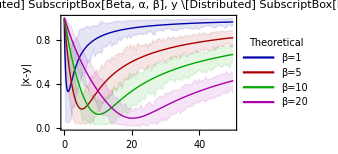

```mathematica
betas = {1,5, 10, 20};
colors = {Blue, Red, Green, Magenta};
betadistpredfig = Legended[Show[Table[Show[
ListLinePlot[
	Transpose[Table[SampleBetaDist[α, betas[[i]],0.25][100], 
		{α, 0.01, 50, 0.5}]],
	Filling->{1->{3}},
	FillingStyle->Opacity[0.1],
	InterpolationOrder->1,
	DataRange->{0, 50},
	PlotTheme->"abestheme", 
	PlotStyle->{
		Directive[Opacity[0.1],Darker[colors[[i]]]], 
		Directive[Opacity[0],Darker[colors[[i]]]], 
		Directive[Opacity[0.1],Darker[colors[[i]]]]}, 
PlotRange->Full],
Plot[dbetas[α, betas[[i]],betas[[i]], α], 
		{α, 0.01, 50},
	PlotStyle->Directive[Darker[colors[[i]]], Thick], 
	PlotTheme->"abestheme", 
	PlotRange->Full]
], {i,4}], ImageSize->250, 
FrameLabel->{"α", "|x-y|"}, 
PlotLabel->"⟨|x-y|⟩_(x \[Distributed] SubscriptBox[Beta, α, β],  y \[Distributed] SubscriptBox[Beta, β, α])"], 
LineLegend[Directive[Darker[#], Thick]&/@{Blue,Red,Green,Magenta},
	Table[Style["β="<>ToString[β], 
		FontFamily->"Times New Roman"], 
		{β, {1,5, 10, 20}}], 
LegendLabel->Style["Theoretical", 
	FontFamily->"Times New Roman", Bold]]]
Export["~/Desktop/betadistpredfig.pdf", 
		betadistpredfig, 
		"AllowRasterization"->True];
```

The between-class distance matrix is therefore:

```mathematica
dmtx[α1_,β1_,α2_,β2_]:=({{dbetas[α1,β1,α1,β1], dbetas[α1,β1,α2,β2]}, {dbetas[α2,β2,α1,β1], dbetas[α2,β2,α2,β2]}});
𝔻[α1_,β1_,α2_,β2_]:=N@dmtx[α1,β1,α2,β2] (*Numerical version*)
𝕊[α1_,β1_,α2_,β2_]:=Exp[-𝔻[α1,β1,α2,β2]]
```

For verification purposes, we define an empirically sampled distance matrix:

```mathematica
SampleDistanceMtx[α_, β_, n1_:100, n2_:100] := 
	Module[{sample1,sample2, dij, dii, djj, dji},
	sample1 = RandomVariate[BetaDistribution[α, β], {n1, 1}];
	sample2 = RandomVariate[BetaDistribution[β, α], {n2, 1}];
	(*dii = Mean[ManhattanDistance[#1, #2]&@@@ RandomVariate[BetaDistribution[α, β], {n1, 2}]];
	dij = Mean[ManhattanDistance[#1, #2]&@@@ RandomVariate[proddist[α, β],n]];
	djj = Mean[ManhattanDistance[#1, #2]&@@@ RandomVariate[BetaDistribution[β, α], {n, 2}]];*)
	dii = Mean@Mean@DistanceMatrix[sample1, sample1, DistanceFunction->ManhattanDistance];
	dij = Mean@Mean@DistanceMatrix[sample1, sample2, DistanceFunction->ManhattanDistance];
	djj = Mean@Mean@DistanceMatrix[sample2, sample2, DistanceFunction->ManhattanDistance];
	({{dii, dij}, {dij, djj}})
	]
```

ANALYTICAL EXPRESSION FOR NUMBERS EQUIVALENT RQE

We begin by defining an analytical expression for RQE:

```mathematica
Q[q_]:=Function[{α1,β1,α2,β2,c}, 
	Module[{p}, 
		p = {1-c, c};
		Total[Total[dmtx[α1, β1, α2, β2]×(p⊗p)^q]]
	]]
```

We verify this against a numerical estimation of RQE:

```mathematica
NumericalRQE[q_, n_:100] := Function[{α1,β1,α2,β2,c}, 
	Module[{p, dii, dij, djj, dist},
	p = {1-c, c};
	dii = Mean[ManhattanDistance[#1, #2] &@@@ 
		RandomVariate[BetaDistribution[α1, β1],{n, 2}]];
	dij = Mean[ManhattanDistance[#1, #2] &@@@ 
		RandomVariate[
			ProductDistribution[
				BetaDistribution[α1, β1], 
				BetaDistribution[α2, β2]],n]];
	djj = Mean[ManhattanDistance[#1, #2] &@@@ 
		RandomVariate[BetaDistribution[α2, β2],{n, 2}]];
	dist = ({{dii, dij}, {dij, djj}});
	Total[Total[dist × (p⊗p)^q]]]]
```

General::munfl: 868.957 5.31211318935622×10^-10647 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 868.957 1.24963378749027×10^-10997 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.59084 8.80062708245324×10^-10619 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

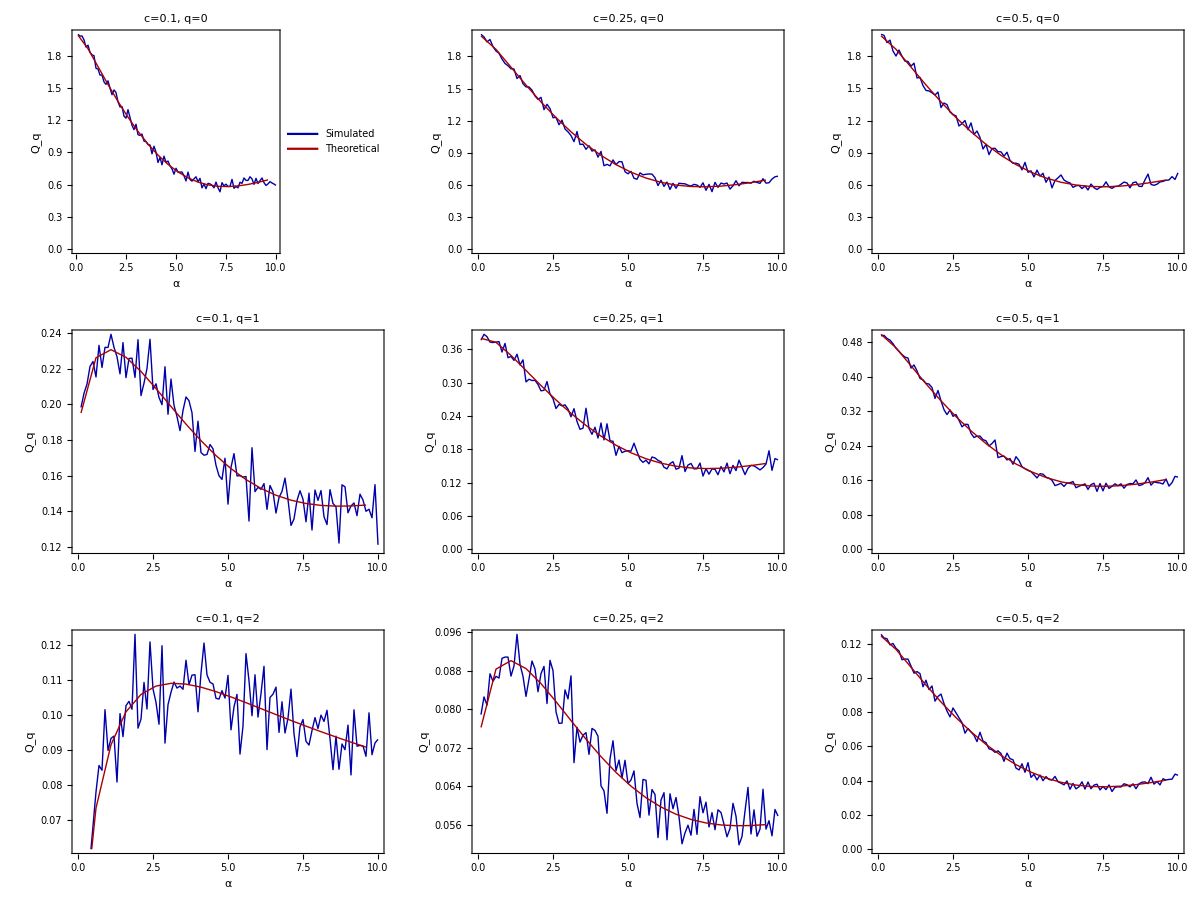

```mathematica
rqeverificationfig = Legended[Grid[Table[ListLinePlot[{
	Table[{α, NumericalRQE[q, 100][α, 7, 7, α,c]},
			{α, 0.1, 10, 0.1}],
	Table[{α, Q[q][α, 7,7,α,c]},{α, 0.1, 10, 0.5}] 
	}, PlotTheme->"abestheme", 
	PlotLabel->Style[
		"c="<>ToString[N[c]]<>", q="<>ToString[q], 
		FontFamily->"Times New Roman"],
	FrameLabel->{"α", "Q_q"}],
{q, {0, 1, 2}}, {c, {1/10,1/4, 1/2}}]], 
LineLegend[{Darker[Blue], Darker[Red]}, 
	Style[#,FontFamily->"Times New Roman"] &/@
		{"Simulated", "Theoretical"}]]
Export["~/Desktop/rqe-verification-fig.pdf", 
	rqeverificationfig, 
	"AllowRasterization"->True];
```

We also normalize RQE for the numbers equivalent version. In the present case this is relatively easy since the distance matrix is symmetrical.

```mathematica
Qneq:=Function[{α1,β1,α2,β2,c},
	Module[{p, dist},
	p = {1-c, c};
	dist = 𝔻[α1, β1, α2, β2];
	dist = (dist-Min[dist])/(Max[dist]-Min[dist]); 
	1/(1-p.dist.p) 
	]
]

NumericalRQEneq[n_:100] := Function[{α1,β1,α2,β2,c}, 
	Module[{p, dii, dij, djj, dist, mindist},
		p = {1-c, c};
		dii = Mean[ManhattanDistance[#1, #2] &@@@ 
			RandomVariate[BetaDistribution[α1, β1], {n, 2}]];
		dij = Mean[ManhattanDistance[#1, #2] &@@@ 
			RandomVariate[ProductDistribution[
				BetaDistribution[α1, β1], 
				BetaDistribution[α2, β2]],n]];
		djj = Mean[ManhattanDistance[#1, #2] &@@@ 
			RandomVariate[BetaDistribution[α2, β2], {n, 2}]];
		dist = ({{dii, dij}, {dij, djj}});
		(*1/(1-p.((dist-Min[dist])/(Max[{dii, dij, djj}]-Min[dist])).p) *)
		1/(1-p.((dist-Min[dist])/(dij-Min[dist])).p) 
	]
]
```

General::munfl: 454761. 4.70815859986079×10^-15518 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 454761. 1.08476391818912×10^-15871 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.59084 6.21660723532223×10^-15475 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

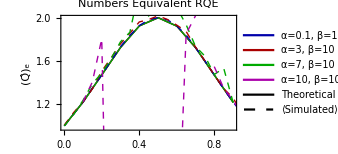

```mathematica
neqrqeverificationfig = Legended[Show[
	ListLinePlot[
		Table[{c, Qneq[α, 10, 10, α, c]},
				{α, {0.1, 3, 7, 10}}, 
				{c, 0.001, 0.999, 0.1}], 
		PlotTheme->"abestheme"], 
	ListLinePlot[
		Table[{c, NumericalRQEneq[250][α, 10, 10, α, c]},
				{α, {0.1, 3, 7, 10}}, 
				{c, 0, 1, 0.05}], 
		PlotStyle-> Dashed, 
		PlotTheme->"abestheme"],
	PlotLabel->"Numbers Equivalent RQE", 
	FrameLabel->{"p[z=2]=c", "(Q̂)_e"}, 
	ImageSize->250], {
LineLegend[Directive[Darker[#], Thick] &/@ 
			{Blue, Red, Green, Magenta}, 
			Table[Style["α="<>ToString[α]<>", β=10", 
				FontFamily->"Times New Roman"], 
				{α, {0.1, 3, 7, 10}}]],
LineLegend[Directive[#, Black]&/@{Thick, Dashed}, 
	Style[#, FontFamily->"Times New Roman"] &/@ 
		{"Theoretical", "⟨Simulated⟩"}]}]
```

For aesthetic purposes, we just include the theoretical values here.

General::munfl: 454761. 4.70815859986079×10^-15518 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 454761. 1.08476391818912×10^-15871 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.59084 6.21660723532223×10^-15475 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

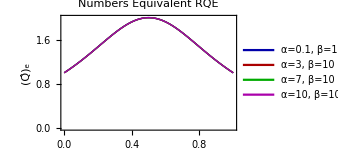

```mathematica
neqrqefig = Legended[Show[
ListLinePlot[
	Table[{c, Qneq[α, 10, 10, α, c]},
			{α, {0.1, 3, 7, 10.01}}, 
			{c, 0, 1, 0.01}], 
		PlotTheme->"abestheme"],
PlotLabel->"Numbers Equivalent RQE", 
FrameLabel->{"p[z=2]=c", "(Q̂)_e"}, 
ImageSize->250], {
LineLegend[Directive[Darker[#], Thick] &/@ 
	{Blue, Red, Green, Magenta}, 
	Table[Style["α="<>ToString[α]<>", β=10", 
	FontFamily->"Times New Roman"], 
	{α, {0.1, 3, 7, 10}}]]
}]
Export["~/Desktop/neqrqefig.pdf", 
		neqrqefig, 
		"AllowRasterization"->True];
```

The functional Hill numbers F_q are

```mathematica
FuncHill[q_]:= Function[{α1,β1,α2,β2,c}, 
	Module[{p, pp, dist},
		p = {1-c, c};
		pp = p ⊗ p;
		dist = dmtx[α1, β1,α2,β2];
		Piecewise[{{(Total[Total[dist × pp^q]]/Total[Total[dist × pp]])^(1/(2(1-q))), q≠1}, {ⅇ^(-1/2 Total[Total[(dist×pp)/Total[Total[dist × pp]] Log[pp]]]), q==1}}] ]
]

NumericalFuncHill[q_, n_:100] := Function[{α1,β1,α2,β2,c}, 
	Module[{p, pp, dii, dij, djj, dist},
		p = {1-c, c};
		pp = p ⊗ p;
		dii = Mean[ManhattanDistance[#1, #2] &@@@ 
			RandomVariate[BetaDistribution[α1, β1], {n, 2}]];
		dij = Mean[ManhattanDistance[#1, #2] &@@@ 
			RandomVariate[ProductDistribution[
				BetaDistribution[α1, β1], 
				BetaDistribution[α2, β2]],n]];
		djj = Mean[ManhattanDistance[#1, #2] &@@@ 
			RandomVariate[BetaDistribution[α2, β2], {n, 2}]];
		dist = ({{dii, dij}, {dij, djj}});
		Piecewise[{{(Total[Total[dist × pp^q]]/Total[Total[dist × pp]])^(1/(2(1-q))), q≠1}, {ⅇ^(-1/2 Total[Total[(dist×pp)/Total[Total[dist × pp]] Log[pp]]]), q==1}}] 
	]
]
```

General::munfl: 454761. 4.70815859986079×10^-15518 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 454761. 1.08476391818912×10^-15871 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.59084 6.21660723532223×10^-15475 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::indet: Indeterminate expression 0.^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

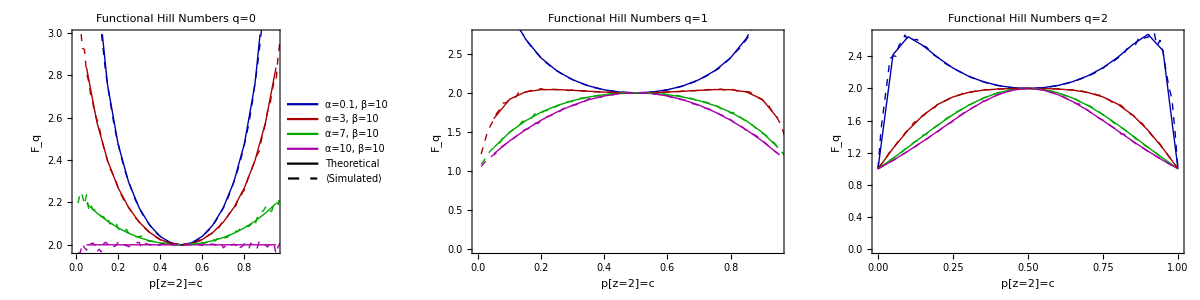

```mathematica
funchillverificationfig = Legended[Grid[{Table[Show[
	ListLinePlot[
		Table[{c, N@FuncHill[q][α, 10, 10, α, c]},
				{α, {0.1, 3, 7, 10}}, 
				{c, 0, 1, 0.05}], 
				PlotTheme->"abestheme"], 
	ListLinePlot[
		Table[{c, NumericalFuncHill[q, 1000][α, 10, 10, α, c]},
				{α, {0.1, 3, 7, 10}}, 
				{c, 0, 1, 0.01}], 
	PlotStyle-> Dashed, 
	PlotTheme->"abestheme"],
	PlotLabel->"Functional Hill Numbers q="<>ToString[q], 
	FrameLabel->{"p[z=2]=c", "F_q"}, 
	ImageSize->250],{q, {0, 1, 2}}]}], {
	LineLegend[Directive[Darker[#], Thick] &/@ 
			{Blue, Red, Green, Magenta}, 
			Table[Style["α="<>ToString[α]<>", β=10", 
						FontFamily->"Times New Roman"], 
				  {α, {0.1, 3, 7, 10}}]], 
	LineLegend[Directive[#, Black] &/@ {Thick, Dashed}, 
		Style[#, FontFamily->"Times New Roman"] &/@ 
		{"Theoretical", "⟨Simulated⟩"}]
}]
Export["~/Desktop/funchillverificationfig.pdf", 
		funchillverificationfig, 
		"AllowRasterization"->True];
```

For aesthetic purposes, we just include the theoretical values here.

General::munfl: 454761. 4.70815859986079×10^-15518 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 454761. 1.08476391818912×10^-15871 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.59084 6.21660723532223×10^-15475 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::indet: Indeterminate expression 0.^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

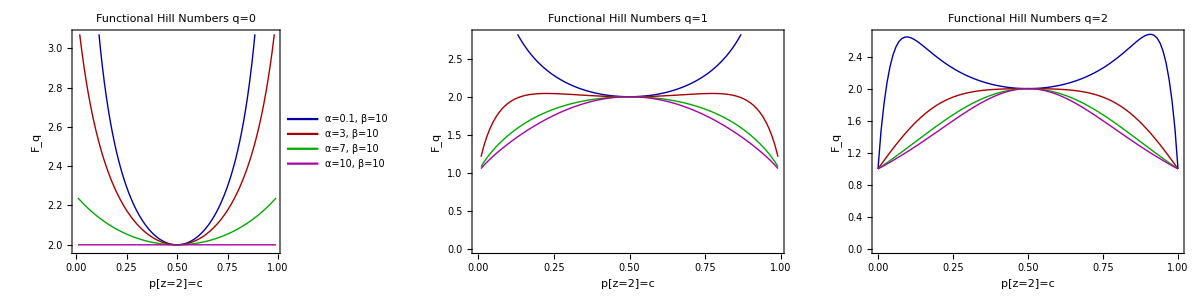

```mathematica
funchilltheoreticalfig = Legended[Grid[{Table[Show[
	ListLinePlot[
		Table[{c, N@FuncHill[q][α, 10, 10, α, c]},
				{α, {0.1, 3, 7, 10}}, 
				{c, 0, 1, 0.01}], 
		PlotTheme->"abestheme"], 
	PlotLabel->"Functional Hill Numbers q="<>ToString[q], 
	FrameLabel->{"p[z=2]=c", "F_q"}, 
	ImageSize->250],{q, {0, 1, 2}}]}], {
LineLegend[Directive[Darker[#], Thick] &/@ 
				{Blue, Red, Green, Magenta}, 
			Table[Style["α="<>ToString[α]<>", β=10", 
				FontFamily->"Times New Roman"], 
			{α, {0.1, 3, 7, 10}}]]
}]
Export["~/Desktop/funchilltheoreticalfig.pdf", 
		funchilltheoreticalfig, 
		"AllowRasterization"->True];
```

The Leinster-Cobbold Index is

```mathematica
LCI[q_][α1_,β1_,α2_,β2_,c_]:= Piecewise[{{({1-c, c}.(𝕊[α1, β1, α2, β2].{1-c, c})^(q-1))^(1/(1-q)), q≠1∧q≠∞}, {Product[((𝕊[α1, β1, α2, β2].{1-c, c})^-q)[[i]], {i, 2}], q==1}, {Min[1/(𝕊[α1, β1, α2, β2].{1-c, c})], q==∞}}]
NumericalLCI[q_, n_:100] := Function[{α1,β1,α2,β2,c}, 
	Module[{p, pp, dii, dij, djj, dist, sim, simp},
		p = {1-c, c};
		pp = p ⊗ p;
		dii = Mean[ManhattanDistance[#1, #2] &@@@ 
			RandomVariate[BetaDistribution[α1, β1], {n, 2}]];
		dij = Mean[ManhattanDistance[#1, #2] &@@@ 
			RandomVariate[ProductDistribution[
				BetaDistribution[α1, β1], 
				BetaDistribution[α2, β2]],n]];
		djj = Mean[ManhattanDistance[#1, #2] &@@@ 
			RandomVariate[BetaDistribution[α2, β2], {n, 2}]];
		dist = ({{dii, dij}, {dij, djj}});
		sim = Exp[-dist];
		simp = sim.p;
		Piecewise[{{(p.(sim.p)^(q-1))^(1/(1-q)), q≠1∧q≠∞}, {(∏_(i=1)^Length[simp] simp[[i]]^-q), q==1}, {Min[1/simp], q==∞}}] ]]
```

General::munfl: 454761. 4.70815859986079×10^-15518 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 454761. 1.08476391818912×10^-15871 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.59084 6.21660723532223×10^-15475 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

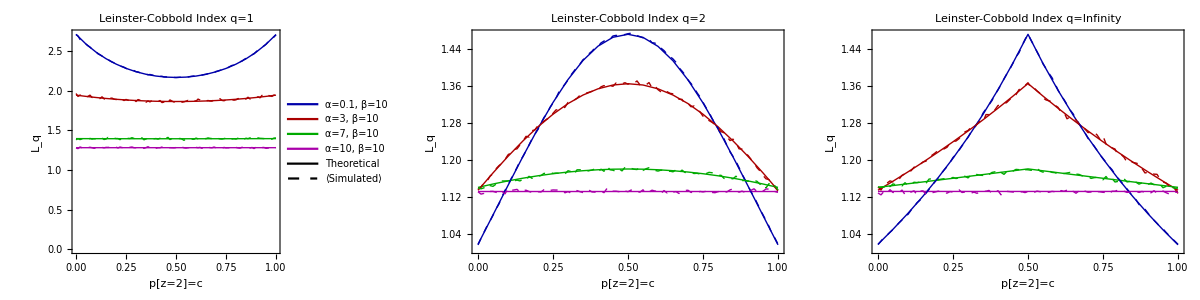

```mathematica
lciverificationfig = Legended[Grid[{Table[Show[
	ListLinePlot[
		Table[{c, N@LCI[q][α, 10, 10, α, c]},
				{α, {0.1, 3, 7, 10}}, 
				{c, 0, 1, 0.05}], 
		PlotTheme->"abestheme"], 
	ListLinePlot[
		Table[{c, NumericalLCI[q, 1000][α, 10, 10, α, c]},
				{α, {0.1, 3, 7, 10}}, 
				{c, 0, 1, 0.01}], 
		PlotStyle-> Dashed, 
		PlotTheme->"abestheme"],
	PlotLabel->"Leinster-Cobbold Index q="<>ToString[q], 
	FrameLabel->{"p[z=2]=c", "L_q"}, 
	ImageSize->250],{q, {1, 2, ∞}}]}], {
LineLegend[Directive[Darker[#], Thick] &/@ 
			{Blue, Red, Green, Magenta}, 
		Table[Style["α="<>ToString[α]<>", β=10", 
				FontFamily->"Times New Roman"], 
			{α, {0.1, 3, 7, 10}}]], 
LineLegend[Directive[#, Black]&/@{Thick, Dashed}, 
			Style[#, FontFamily->"Times New Roman"] &/@ 
				{"Theoretical", "⟨Simulated⟩"}]}]

Export["~/Desktop/lciverificationfig.pdf", 
		lciverificationfig, 
		"AllowRasterization"->True];
```

For aesthetic purposes, we just include the theoretical values here.

General::munfl: 454761. 4.70815859986079×10^-15518 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 454761. 1.08476391818912×10^-15871 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.59084 6.21660723532223×10^-15475 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

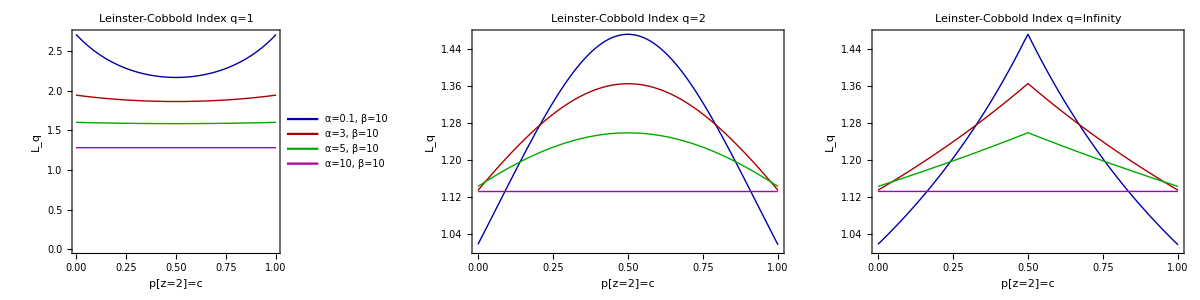

```mathematica
lcitheoreticalfig = Legended[Grid[{Table[Show[
	ListLinePlot[
		Table[{c, N@LCI[q][α, 10, 10, α, c]},
				{α, {0.1, 3, 5, 10}}, 
				{c, 0, 1, 0.01}],
		PlotTheme->"abestheme"], 
	PlotLabel->"Leinster-Cobbold Index q="<>ToString[q], 
	FrameLabel->{"p[z=2]=c", "L_q"}, 
	ImageSize->250],{q, {1, 2, ∞}}]}], {
	LineLegend[Directive[Darker[#], Thick] &/@ 
				{Blue, Red, Green, Magenta}, 
			  Table[Style["α="<>ToString[α]<>", β=10", 
			  FontFamily->"Times New Roman"], 
			  {α, {0.1, 3, 5, 10}}]]
}]

Export["~/Desktop/lcitheoreticalfig.pdf", 
		lcitheoreticalfig, 
		"AllowRasterization"->True];
```

The representational Rényi heterogeneity for comparison is

```mathematica
rhettheoreticalfig = Legended[Grid[{Table[Show[
	ListLinePlot[
		Table[{c, renyihet[q, α,10.0001,c][thresh[α,10.0001,c]]},
				{α, {0.1, 3, 7, 10}}, 
				{c, 0, 1, 0.01}],
		PlotTheme->"abestheme", PlotRange->Full], 
	PlotLabel->"Representational Rényi q="<>ToString[q], 
	FrameLabel->{"p[z=2]=c", "Π_q"}, 
	ImageSize->250],{q, {1, 2, ∞}}]}], {
	LineLegend[Directive[Darker[#], Thick] &/@ 
				{Blue, Red, Green, Magenta}, 
			  Table[Style["α="<>ToString[α]<>", β=10", 
			  FontFamily->"Times New Roman"], 
			  {α, {0.1, 3, 7, 10}}]]
}]; 
Export["~/Desktop/rhettheoreticalfig.pdf", 
		rhettheoreticalfig, 
		"AllowRasterization"->True];
```

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^0.0505045 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::munfl: 1/99.^5000. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.01^5000. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/49.^5000. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

A grid of comparisions across values of q and different BMM distributions is shown as follows:

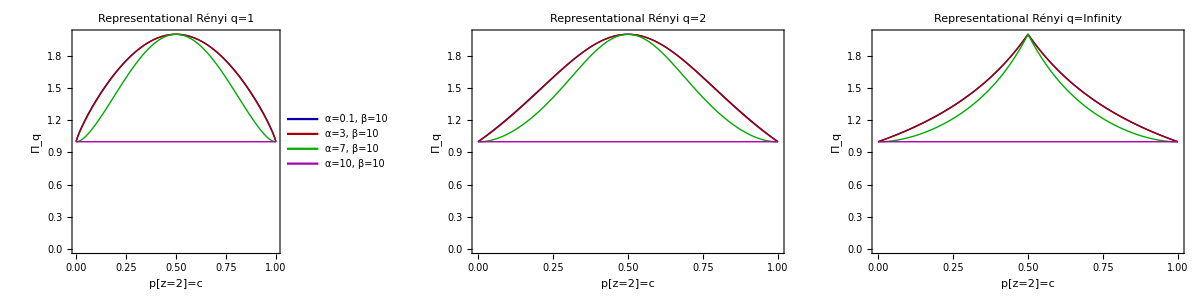
-Graphics-
-Graphics-
-Graphics-

```mathematica
rrhfhnrqelcigrid = Grid[{
		{rhettheoreticalfig}, 
		{funchilltheoreticalfig}, 
		{lcitheoreticalfig}}]
Export["~/Desktop/rrhfhnrqelcigrid.pdf", 
		rrhfhnrqelcigrid, 
		"AllowRasterization"->True];
```

Figure XX compares the categorical representational Rényi heterogeneity (using the hard thresholding method) against (Q̂)_e, F_q, and L_q for BMM distributions of varying degrees of separation, and across different mixture component weights (0≤c≤1). For parsimony, we show only those comparisons at q=2, but further comparisons are provided in Appendix XX.  

The most salient differences between these indices occur when the BMM mixture components completely overlap (i.e. at α=β). The representational Rényi heterogeneity correctly identifies that there is effectively only one component, regardless of mixture weights. Only the Leinster-Cobbold index showed invariance to the mixture weights when α=β, but it could not correctly identify that data were effectively unimodal. 

The other stark difference arose when the mixture components were furthest apart (here when α=0.1 and β=10). At this setting, the functional Hill numbers showed a paradoxical increase in the heterogeneity estimate as the prior distribution on components was skewed. The Leinster-Cobbold index was appropriately concave throughout the range of prior weights, but it never reached a value of 2 at its peak (as expected based on the predictions outlined in section Leinster-Cobbold Index). Conversely, the representational Rényi heterogeneity was always concave and reached a peak of 2 when both mixture components were equally probable.

Finally, we can observe that the numbers equivalent RQE was insensitive to separation of the mixture components. This is a particularly important problem when the components overlap completely, since that would suggest that the distribution on 𝒳 is effectively unimodal.

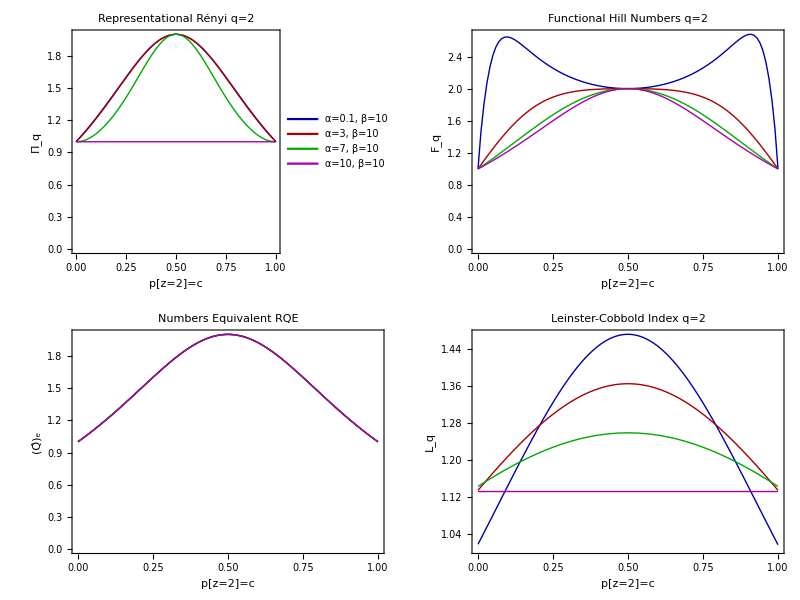

```mathematica
rrhcatgrid = Legended[Grid[{
	{rhettheoreticalfig[[1,1,1,2]], funchilltheoreticalfig[[1,1,1,3]]}, 
	{neqrqefig[[1]], lcitheoreticalfig[[1,1,1,2]]}}], 
	Placed[neqrqefig[[2,1]], {0.22, 0.15}]]
Export["~/Desktop/rrhcatgrid.pdf", 
		rrhcatgrid, 
		"AllowRasterization"->True];
```

Overall, we believe that the categorical representational Rényi heterogeneity (here using a hard thresholding approach to cluster assignment) is overall a more consistently behaved measure of heterogeneity than the evaluated comparators. The representational Rényi heterogeneity was sensitive to BMM component separation, and was the only index to correctly identify an effectively unimodal BMM. Our measure was also always concave (unlike the functional Hill numbers), and consistently identified bimodality when distributions were not completely overlapping and equally weighted.

## Heterogeneity of Learned Non-Categorical Representations

In many cases, the most appropriate latent representation for our observable data will be continuous, in which the Rényi heterogeneity is computed as

Π_q[z\[Conditioned]X]=(∫_𝒵 p_θ^q[z\[Conditioned]X]ⅆz)^(1/(1-q)).

In the two-component BMM example shown in the previous section, we were able to simplify the computation by mapping observations onto the latent space using a hard threshold. This is not possible in the non-categorical setting.  Instead, we present a method based on the Rényi heterogeneity decomposition procedure outlined by Jost (2007). As an example system that is decidedly more complex than the 2-component BMM, we consider a convolutional variational autoencoder (cVAE; Kingma & Welling, 2014) which we apply to the MNIST dataset of handwritten digit images (LeCun et al. 1998). However, the procedure we employ herein may be generalized to other distributions.

A VAE is made up of an encoder and a decoder (Figure XX), which together aim to learn a compressed latent representation that can reconstruct the respective input data. In the convolutional VAE model, the encoder consists of a convolutional neural network whose output layer encodes the mean (μ(X)) and diagonal covariance (σ(X)) functions for a Gaussian distribution over latent representation vector z∈𝒵^(n_z×n_z). The dimension of 𝒵 is typically much smaller than that of the input space 𝒳. The decoder of a cVAE consists of a neural network whose input is a latent representation vector z, and whose output is a reconstruction of some input data. For more details, see Kingma & Welling (2014). In the present study, the input data consist of 28-by-28 binary images, and the latent space is set to a dimension of n_z=2 for simplicity. Computing the representational Rényi heterogeneity requires us to derive a parametric form for Π_q[z\[Conditioned]X] on the latent space, which for the cVAE translates into computing Π_q[Encoder].

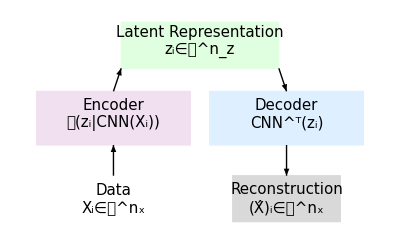

```mathematica
vaefig = Show[
	Graphics[{EdgeForm[{Thick}], White, Rectangle[{0.3, 0}, {1.7, 0.6}]}],
	Graphics[{EdgeForm[{Thick}], LightPurple, Rectangle[{0, 1}, {2, 1.7}]}],
	Graphics[{EdgeForm[{Thick}], LightGreen, Rectangle[{1.1, 2}, {3.15, 2.6}]}],
	Graphics[{EdgeForm[{Thick}], LightBlue, Rectangle[{2.25, 1}, {4.25, 1.7}]}],
	Graphics[Text[Style["Latent Representation\nz_i∈𝒵^n_z", 15], {2.125, 2.35}]],
	Graphics[Text[Style["Data\nX_i∈𝒳^n_x", 15], {1, 0.3}]],
	Graphics[Text[Style["Decoder\nCNN^ᵀ(z_i)", 15], {3.25, 1.4}]],
	Graphics[Text[Style["Encoder\n𝒩(z_i|CNN(X_i))", 15], {1, 1.4}]],
	Graphics[{Thick, Arrow[{{1, 0.6}, {1, 1}}]}],
	Graphics[{EdgeForm[{Thick}], LightGray, Rectangle[{2.55, 0}, {3.95, 0.6}]}],
	Graphics[Text[Style["Reconstruction\n(X̂)_i∈𝒳^n_x", 15], {3.25, 0.3}]],
	Graphics[{Thick, Arrow[{{3.25, 1}, {3.25, 0.6}}]}],
	Graphics[{Thick, Arrow[{{1, 1.7}, {1.1, 2}}]}],
	Graphics[{Thick, Arrow[{{3.15, 2}, {3.25, 1.7}}]}],
BaseStyle->{FontFamily->"Times New Roman"}]
Export["~/Desktop/vaefig.pdf", 
		vaefig, 
		"AllowRasterization"->True];
```

### Deriving Continuous Representational Rényi Heterogeneity for the cVAE

The Rényi heterogeneity of the space captured by our dataset X=(x_i)_(i=1,2,...,n_s) corresponds to the effective number of observations. For example, if every element of X is identical, then the Rényi heterogeneity should be 1. However, greater variation in X corresponds to an increase in the effective number of completely distinct observations. Since the encoder generates a Gaussian distribution for each observation x_i, the latent representation of the whole dataset is a Gaussian mixture model with equal weights (since we assume a uniform distribution on each observation). One can show that the Rényi heterogeneity for a multivariate Gaussian is

Π_q[Σ_i]=Piecewise[{{(2π )^(n/2)q^(n/(2(q-1)))√(det(Σ_i)), q≠1∧q≠∞∧q≠0}, {(2π ⅇ)^(n/2)√(det(Σ_i)), q=1}, {(2π)^(n/2)√(det(Σ_i)), q=∞}, {Undefined, q=0}}]

where Σ_i is the covariance function given observation x_i. The projection of all observations onto the latent space results in a mixture of Gaussians with pooled covariance matrix

Σ̃=⟨Σ⟩ + ⟨μ μ^ᵀ⟩-⟨μ ⟩⟨μ⟩^ᵀ

where μ is the mean function given some input data (indices omitted for parsimony), and ⟨·⟩ denotes expectation over all observations. The representational Rényi heterogeneity over the pooled dataset is simply Π_q^Pooled[Σ̃]. As proven by Jost (2007), the pooled Rényi heterogeneity can be decomposed as follows

(Π_q^Pooled[Σ̃])_Overall=(Π_q^Within[Σ_(i=1,2,...,n_s)])_(Within-observation heterogeneity) (Π_q^Between[Σ_(i=1,2,...,n_s)])_(Between-observation heterogeneity).

The overall, within-, and between-observation heterogeneity values all have units of numbers equivalent, but we are interested primarily in the between-observation value, since it returns the effective number of observations. Conversely, the within-observation heterogeneity is more of a description of the model’s uncertainty regarding the latent representation of input data. For the mixture of Gaussians model, the between-observation heterogeneity can be easily computed as follows:

Π_q^Between[Σ_(i=1,2,...,n_s)]=Π_q^Pooled[Σ̃]/Π_q^Within[Σ_(i=1,2,...,n_s)]=Piecewise[{{√(det(Σ̃))(1/n_s∑_(i=1)^n_s det(Σ_i)^((1-q)/2))^(1/(q-1)), q≠1}, {√(det(Σ̃))(∏_(i=1)^n_s det(Σ_i)^(1/(2 n_s)))^-1, q=1}}].

### Empirical Evaluation on MNIST

A pre-trained cVAE (http://geometry.cs.ucl.ac.uk/creativeai) was employed for the empirical evaluation. 

We began by projecting the 60,000 MNIST training images (some samples are shown in Figure XXA) into the latent space and computing the pooled, within-observation, and between-observation Rényi heterogeneity according to the handwritten digit label (Figure XXB). To evaluate each digit’s contribution to the representational Rényi heterogeneity of the aggregated dataset, we recomputed the Rényi heterogeneity on the aggregated data with each of the digit classes left out (Figure XXC).

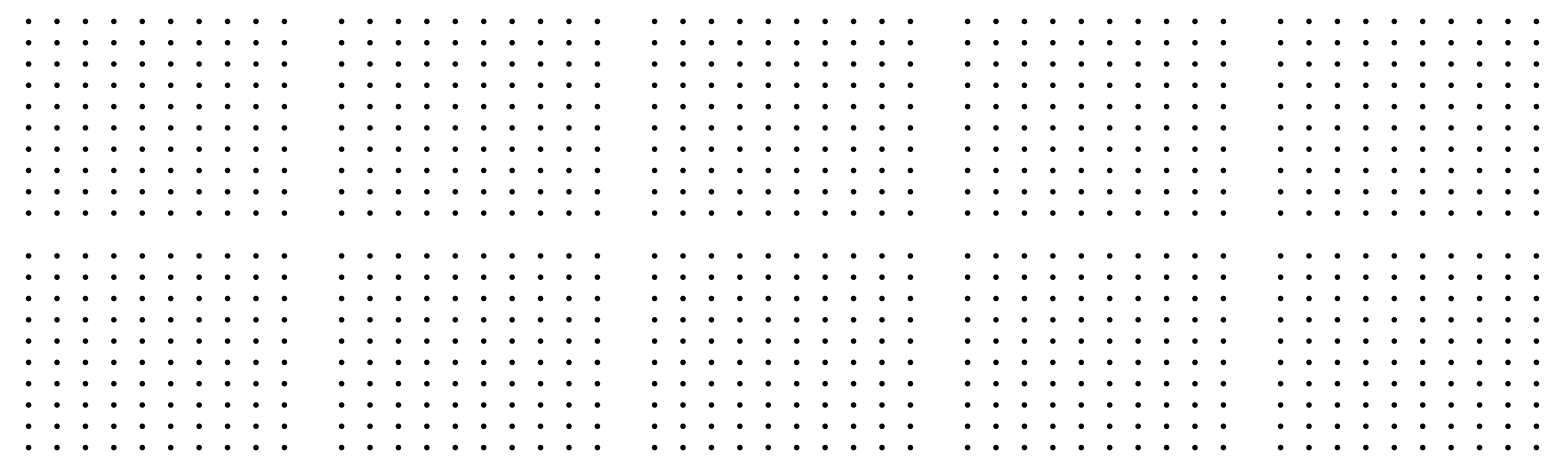
(A) Samples from the MNIST Dataset
-Graphics-
(B) Representational Rényi Heterogeneity for Each Digit Class
-Graphics-
(C) Representational Rényi Heterogeneity with Each Digit Class Excluded
-Graphics-

```mathematica
trainingData = ResourceData["MNIST", "TrainingData"];
mnistgrid = Grid[ArrayReshape[
	Table[GraphicsGrid[
		ArrayReshape[
			RandomSample[
				Select[trainingData, #[[2]] == i&], 
				100][[All, 1]], 
			{10, 10}], 
		ImageSize->Tiny], {i, 0, 9}], {2, 5}]];
Export[imgdir<>"mnistgrid.pdf", 
		mnistgrid, 
		"AllowRasterization"->True];


rrhdigitgrid = Grid[{
	{Style["(A) Samples from the MNIST Dataset", Bold, 15, FontFamily->"Times New Roman"]},
	{mnistgrid},
	{Style["(B) Representational Rényi Heterogeneity for Each Digit Class", Bold, 15, FontFamily->"Times New Roman"]},
	{Import[imgdir<>"digit-class-heterogeneity.pdf"][[1]]},
	{Style["(C) Representational Rényi Heterogeneity with Each Digit Class Excluded", Bold, 15, FontFamily->"Times New Roman"]},
	{Import[imgdir<>"digit-class-heterogeneity-loco.pdf"][[1]]} 
	}]
Export[imgdir<>"digit-class-heterogeneity-grid.pdf", 
		rrhdigitgrid, 
		"AllowRasterization"->True];
```

Figures XXB and C demonstrate some important properties of the representational Rényi heterogeneity. First, it highlights the importance of using between-observation heterogeneity as the statistic of interest. In the MNIST dataset, one may appreciate that the class of handwritten “ones” is generally the most homogeneous (being for the most part a single straight line). If one was to use the pooled or within-observation statistics as the heterogeneity measure, the opposite conclusion would be drawn. 

Second, and somewhat paradoxically, Figure XXC shows that removal of images of “ones” (the class with the smallest effective number of observations in Figure XXB) from the dataset results in one of the greatest reductions in the between-observation heterogeneity of the remaining data. Conversely, removing the images of “fives” (the class with the largest effective number of observations in Figure XXB) results in a small increase in overall heterogeneity. How can removal of an effectively large subset of images (i.e. one with a high between-observation heterogeneity) increase the amount of heterogeneity in the remaining sample? On the same note, how can removal of the effectively smallest subset of images (i.e. the relatively homogeneous “ones”) result in one of the largest reductions of heterogeneity in the overall sample?

### A Representational Heterogeneity Map

Figure XXA shows a visualization of the 2-dimensional latent space in our cVAE and samples from regions with different levels of between-observation heterogeneity. The digit classes whose exclusion from the aggregate dataset results in increased between-observation heterogeneity can clearly be seen to occupy the peripheries of the latent space (i.e. the “tails” of the latent multivariate Gaussian). 

We then sought to “map” the relative amounts of pooled, within-, and between-observation heterogeneity encoded in the latent space. This was done by (A) reconstructing 49 images for each square M×M neighbourhood of latent coordinates, then (B) projecting those samples back into the latent space, where the between-observation heterogeneity was recalculated. Figure XXA shows eight such instances, wherein one can appreciate that the between-observation heterogeneity indeed tracks visually appreciable sample diversity.

```mathematica
latentmap = Import[imgdir<>"latent-space-map.tif"];
betasamples = Import[imgdir<>"beta-heterogeneity-samples.tif"];
betamap = Import[imgdir<>"heterogeneity-map.pdf"][[1]];
colorbar = Magnify[Import[imgdir<>"colorbar.png"],2];

grida = GraphicsGrid[{
	{latentmap, betasamples, 
		SpanFromLeft, SpanFromLeft, SpanFromLeft}}, 
	ImageSize->800, Spacings->-125];
	
mapgrid = Grid[{{
Style["(A) Latent Space Map and Samples with different Between-Observation Heterogeneity", 
		Bold, 15, FontFamily->"Times New Roman"]},
{grida},{},{
Style["(B) Pooled, Within, and Between-Observation Heterogeneity across the Latent Space", 
		Bold, 15, FontFamily->"Times New Roman"]}, {betamap}, {colorbar}}]
		
Export[imgdir<>"heterogeneity-map-grid.pdf", 
		mapgrid, 
		"AllowRasterization"->True];
```

(A) Latent Space Map and Samples with different Between-Observation Heterogeneity
-Graphics-

(B) Pooled, Within, and Between-Observation Heterogeneity across the Latent Space
-Graphics-
-Graphics-

The resulting latent-space heterogeneity maps are shown in Figure XXB.  Here, one can appreciate that the cVAE encodes the bulk of its sample diversity in the center of the latent space, with more homogeneous subgroups encoded in the peripheries. These data suggest a potential mechanism for the paradox observed in Figure XXC: that the continuous representational Rényi heterogeneity is driven by extreme-valued subsets of the data. In our MNIST example, we can observe that the “ones, sixes, and zeros” are sufficiently distinct from the other digits such that they are pushed to the distribution’s tails, which increases the overall between-observation heterogeneity. In other words, we hypothesize that the representational Rényi heterogeneity primarily captures the existence of (A) multimodality and (B) respective modes’ deviance.

### The Deviant Mode Hypothesis and Classical Functional Diversity Indices

To test the hypothesis that representational Rényi heterogeneity is primarily driven by the existence of deviant modes, we performed a simple simulation experiment. First, we arranged 20 bivariate Gaussian distributions (with equal variance) along a straight line. We then measured the resulting mixture distribution’s heterogeneity (using our representational Rényi form, as well as (Q̂)_e, F_q, and L_q) in response to pruning mixture components either (A) from the center of the distribution outward, or (B) from the tails inward. This process is depicted in Figure XXA.

```mathematica
deviantmodefig = Grid[{
{Style["(A) Depiction of the Mode-Pruning Experimental Protocol", 
		Bold, 15, FontFamily->"Times New Roman"]}, 
{Import[imgdir<>"mode-pruning-illustration.pdf"][[1]]}, 
{Style["(B) Effect of Mode Pruning on Representational Rényi Heterogeneity", 
		Bold, 15, FontFamily->"Times New Roman"]}, 
{Import[imgdir<>"mode-removal-beta-heterogeneity.pdf"][[1]]}, 
{Style["(C) Effect of Mode Pruning on Existing Heterogeneity Indices", 
		Bold, 15, FontFamily->"Times New Roman"]}, 
{Import[imgdir<>"classic-index-mode-pruning.pdf"][[1]]}}]
Export[imgdir<>"deviantmodegrid.pdf", 
		deviantmodefig, 
		"AllowRasterization"->True]
```

(A) Depiction of the Mode-Pruning Experimental Protocol
-Graphics-
(B) Effect of Mode Pruning on Representational Rényi Heterogeneity
-Graphics-
(C) Effect of Mode Pruning on Existing Heterogeneity Indices
-Graphics-

~/Documents/papers/physical-review-e-heterogeneity/deviantmodegrid.pdf

As expected under our deviant mode hypothesis, pruning mixture components from the centre outward will increase the representational Rényi heterogeneity, while the opposite effect is observed when mixture components are pruned from the tails inward. Conversely, the functional Hill number decreases by a constant amount for every mode removed, regardless of whether pruning occurred centrally or at the tails. A similar monotonic decrease was observed for the Leinster-Cobbold index, although tail pruning resulted in a greater reduction of heterogeneity than central mode pruning. Interestingly, the Numbers equivalent RQE increased with both central and tail mode pruning.

## Discussion

However, using the representational Rényi heterogeneity requires us to understand the nature of the latent representations and their probability distributions.

## Limitations

In our analysis of measuring heterogeneity on learned categorical spaces, we assumed that the BMM was initialized with 2 components. In reality, selecting the correct number of components for a finite mixture model or clustering algorithm otherwise is a challenging problem. Several solutions exist, including comparison of approximations to the model evidence, and using random process priors on the component number. However, the Rényi heterogeneity is computed after the mixture model is learned, and so our results are likely generalizable to both cases. 

Our analysis of heterogeneity measurement on learned categorical spaces is also limited by the focus on a unidimensional model with only two component distributions. However, this limitation is tempered by the fact that our analyses were exact, and that we provided  supplementary simulation-based analysis in multiple dimensions. Future studies should generalize our results into multiple dimensions and larger component numbers, while retaining clarity and brevity of presentation.

## References

Botta-Dukát Z. The generalized replication principle and the partitioning of functional diversity into independent alpha and beta components. Ecography (Cop). 2018;41(1):40–50.

Chiu CH, Chao A. Distance-based functional diversity measures and their decomposition: A framework based on hill numbers. PLoS One. 2014;9(7).

Crooks GE. On measures of entropy and information. Tech Note 009 v0.7. 2018.

Daly A, Baetens J, De Baets B. Ecological Diversity: Measuring the Unmeasurable. Mathematics. 2018;6(7):119.

Eliazar II, Sokolov IM. Measuring statistical evenness: A panoramic overview. Phys A Stat Mech its Appl. 2012;391(4):1323–53.

Hill MO. Diversity and Evenness: A Unifying Notation and Its Consequences. Ecology. 1973;54(2):427–32.

Jost L. Entropy and diversity. Oikos. 2006;113:363–75.

Jost L. Partitioning Diversity into Independent Alpha and Beta Components. Ecology. 2007;88(10):2427–39.

Jost L. The relation between evenness and diversity. Diversity. 2010;2(2):207–32.

Kingma DP and Welling, M. Autoencoding Variational Bayes. ICLR 2014 (2014),
arXiv:arXiv:1312.6114v10.

Laakso M, Taagepera R. “Effective” number of parties: A Measure with Application to West Europe. Comp Polit Stud. 1979 Apr;12(1):3–27.

LeCun, Y and Bottou, L and Bengio, Y and Haffner, P. Gradient-based learning applied to document recognition. Proceedings of the IEEE. 1998; 86: 2278–2324

Nunes A, Trappenberg T, and Alda M. The Meaning and Measure of Heterogeneity. Currently under peer review. 2019

Patil AGP, Taillie C. Diversity as a Concept and its Measurement. J Am Stat Assoc. 1982;77(379):548–61.

Rao CR. Diversity and dissimilarity coefficients: A unified approach. Theor Popul Biol. 1982;21(1):24–43.

Ricotta C, Szeidl L. Diversity partitioning of Rao’s quadratic entropy. Theor Popul Biol. 2009;76(4):299–302.

Shannon CE. A mathematical theory of communication. Bell Syst Tech J. 1948;27(July 1928):379–423.

Simpson EH. Measurement of Diversity. Nature. 1949;163(1943):688.